# Direct Detection limits from lux

```mathematica
SetDirectory["/media/vanniagm/36887AD4887A925B/nu_portal/MATH_NUMODEL/"];
```

List of model parameters

#### Relative Abundance

#### Ω=0.1198+-0.0026

```mathematica
Ωexp = 0.1198; Ωerr = 0.0026; 
vev = 246; 
time1 = SessionTime[];
```

#### Abundance Plot

Degenerate masses case, mphi~mpsi for mpsi > 62  Both cases , deg. and non - deg are included for mpsi < 62

```mathematica
omf2G=Join[Import["mpsi_1_200.dat"],Import["mpsims.840.dat"],Import["mpsims.1550.dat"],Import["mpsims.1000.dat"],Import["mpsims.850.dat"],Import["mpsims.1260.dat"],Import["mpsims.810.dat"],Import["mpsims.920.dat"],Import["mpsims.930.dat"],Import["mpsims.1300.dat"],Import["mpsims.925.dat"],Import["mpsims.825.dat"],Import["mpsims.1270.dat"]];Length[omf2G]
```

195914

```mathematica
oml=SortBy[omf2G,#[[1]]&];Length[oml]
```

195914

```mathematica
om=oml;
```

```mathematica
om1=Table[If[om[[i,1]]≤46&&om[[i,6]]==1,om[[i]],Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[om1]
om1d=Table[If[om[[i,1]]≤46&&om[[i,6]]<1,om[[i]],Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[om1d]
```

78478

83065

```mathematica
om2=Table[If[om[[i,1]]≥48&&om[[i,6]]==1,om[[i]],Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[om2]
om2d=Table[If[om[[i,1]]≥48&&om[[i,6]]<1,om[[i]],Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[om2d]
```

5789

28582

```mathematica
om2d[[2]]
om1[[2]]
```

{54.5,2675.,315.2,315.2,0.6,0.8534,0.12745,7.534×10^-45,8.335×10^-47,3.001×10^-45,3.3788×10^8,0.55478,5.583,2.401,0.0068331,0.02924}

{2.5,1685.,193.9,193.9,-0.3,1.,0.12698,3.4302×10^-45,5.6858×10^-47,9.8076×10^-46,1.3605×10^8,0.00048434,0.12982,2.4014,0.0062464,0.03151}

```mathematica
om22=Table[If[om[[i,1]]≥48,{om[[i]],(om[[i,3]]/om[[i,2]])^2},Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[om2]
```

5789

```mathematica
om22[[22959]]
```

{{62.5,7723.,897.,897.,0.,0.8707,0.12543,1.011×10^-44,1.126×10^-46,4.028×10^-45,4.3817×10^8,0.88918,7.976,2.4013,0.0066333,0.},0.01349}

```mathematica
omz=Table[If[om[[i,1]]≥40&&om[[i,1]]<48&&om[[i,6]]==1,om[[i]],Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[omz]
omzd=Table[If[om[[i,1]]≥40&&om[[i,1]]<48&&om[[i,6]]<1,om[[i]],Unevaluated[Sequence[]]],{i,1,Length[om]}];Length[omzd]
```

2196

2184

Direct Detection

```mathematica
Region compatible with Planck and Lux
```

and compatible Lux Planck Region with

```mathematica
Get["/media/vanniagm/36887AD4887A925B/nu_portal/MATH_NUMODEL/xenon1T_lux16.m"]
```

InterpolatingFunction::dmval: Input value {60.5566} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {646.629} lies outside the range of data in the interpolating function. Extrapolation will be used.

/media/vanniagm/36887AD4887A925B/nu_portal

```mathematica
ptsAbLuxND=Table[If[om1[[i,10]]<σlux16[om1[[i,1]]],om1[[i]],Unevaluated[Sequence[]]],{i,1,Length[om1]}];
```

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {36.354} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {36.354} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {561.617} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
ptsAbLuxND2=Table[If[om2[[i,10]]<σlux16[om2[[i,1]]],om2[[i]],Unevaluated[Sequence[]]],{i,1,Length[om2]}];
```

```mathematica
ptsAbLuxD=Table[If[om1d[[i,10]]<σlux16[om1d[[i,1]]],om1d[[i]],Unevaluated[Sequence[]]],{i,1,Length[om1d]}];
```

InterpolatingFunction::dmval: Input value {-10.7961} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
ptsAbLuxD2=Table[If[om2d[[i,10]]<σlux16[om2d[[i,1]]],om2d[[i]],Unevaluated[Sequence[]]],{i,1,Length[om2d]}];
```

InterpolatingFunction::dmval: Input value {259.203} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
ptsAbLuxD[[Length[ptsAbLuxD]]]
```

{30.5,1091.,121.2,121.2,-0.6,0.7606,0.11748,1.8936×10^-45,3.9801×10^-46,3.0115×10^-46,1.289×10^8,0.085574,1.4091,2.402,0.0076071,0.2047}

{2.,1091.,36.36,36.36,0.,0.1683,0.1276,3.7836×10^-47,6.9231×10^-50,1.23×10^-47,24108.,3.9411×10^-8,0.000015981,2.4094,0.0060499,0.00005106}

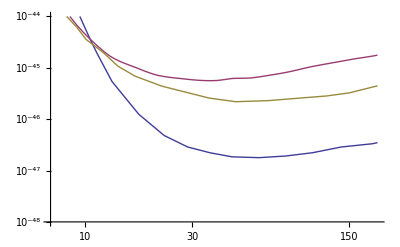

```mathematica
LogLogPlot[{xenon1t[m],lux15[m],σlux16[m]},{m,7,200},PlotRange->{10^-48,10^-44}]
```

```mathematica
ms11=Table[If[om1d[[i,1]]≤40,{om1d[[i,1]],om1d[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1d]}];
ms12=Table[If[om1[[i,1]]≤40,{om1[[i,1]],om1[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om1]}];
ms21=Table[If[om2d[[i,1]]>=48,{om2d[[i,1]],om2d[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om2d]}];
ms22=Table[If[om2[[i,1]]>=48,{om2[[i,1]],om2[[i,10]]},Unevaluated[Sequence[]]],{i,1,Length[om2]}];
```

```mathematica
msz1=Table[{omzd[[i,1]],omzd[[i,10]]},{i,1,Length[omzd]}];
msz2=Table[{omz[[i,1]],omz[[i,10]]},{i,1,Length[omz]}];
```

```mathematica
sigmpsinoncoh=Table[{om1[[i,1]],om1[[i,10]]},{i,1,Length[om1]}];
sigmpsinoncoh2=Table[{om2[[i,1]],om2[[i,10]]},{i,1,Length[om2]}];
```

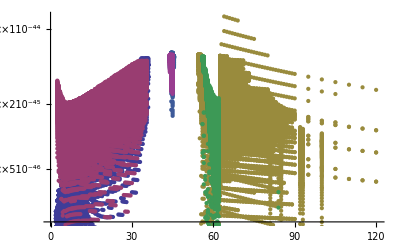

```mathematica
ListLogPlot[{ms11,ms12,ms21,ms22,msz1,msz2}]
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[ms11[[All,{1,2}]],First]
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[ms11[[All,{1,2}]],First]
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->1];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->1]
```

{{1.,1.6238×10^-51},{1.5,1.7406×10^-51},{2.,2.3952×10^-53},{2.5,8.3459×10^-57},{3.,8.8537×10^-52},{3.5,1.0935×10^-52},{4.,9.8303×10^-51},{4.5,6.9553×10^-51},{5.,9.7809×10^-50},{5.5,2.3648×10^-51},{6.,2.5219×10^-50},{6.5,7.491×10^-50},{7.,5.3984×10^-50},{7.5,3.1298×10^-49},{8.,2.7463×10^-49},{8.5,1.536×10^-52},{9.,3.8913×10^-47},{9.5,9.552×10^-49},{10.,1.0114×10^-48},{10.5,2.5163×10^-48},{11.,2.5891×10^-48},{11.5,1.8686×10^-47},{12.,1.8796×10^-47},{12.5,2.9853×10^-47},{13.,2.9854×10^-47},{13.5,1.477×10^-47},{14.,1.4851×10^-47},{14.5,6.1839×10^-47},{15.,5.0074×10^-47},{15.5,5.0077×10^-47},{16.,6.2981×10^-47},{16.5,6.2801×10^-47},{17.,7.7835×10^-47},{17.5,7.7724×10^-47},{18.,4.9669×10^-47},{18.5,4.9609×10^-47},{19.,4.9546×10^-47},{19.5,1.1858×10^-46},{20.,1.1829×10^-46},{20.5,1.262×10^-46},{21.,1.2567×10^-46},{21.5,2.1798×10^-46},{22.,1.7885×10^-46},{22.5,1.783×10^-46},{23.,1.7775×10^-46},{23.5,2.482×10^-46},{24.,2.4732×10^-46},{24.5,3.2142×10^-46},{25.,1.3611×10^-46},{25.5,1.3563×10^-46},{26.,1.3515×10^-46},{26.5,1.8581×10^-46},{27.,2.4676×10^-46},{27.5,2.4563×10^-46},{28.,2.4451×10^-46},{28.5,3.6145×10^-46},{29.,3.5968×10^-46},{29.5,4.7615×10^-46},{30.,3.0213×10^-46},{30.5,3.0115×10^-46},{31.,3.0019×10^-46},{31.5,2.9923×10^-46},{32.,3.9209×10^-46},{32.5,4.8561×10^-46},{33.,5.7849×10^-46},{33.5,7.6253×10^-46},{34.,8.5043×10^-46},{34.5,1.0235×10^-45},{35.,1.1051×10^-45},{35.5,1.3473×10^-45},{36.,1.8692×10^-45}}

{{1.,7.9252×10^-47},{1.5,1.31×10^-46},{2.,2.001×10^-46},{2.5,2.515×10^-46},{3.,3.119×10^-46},{3.5,3.172×10^-46},{4.,3.851×10^-46},{4.5,4.272×10^-46},{5.,4.735×10^-46},{5.5,4.641×10^-46},{6.,5.11×10^-46},{6.5,5.641×10^-46},{7.,6.247×10^-46},{7.5,5.877×10^-46},{8.,6.905×10^-46},{8.5,7.382×10^-46},{9.,7.324×10^-46},{9.5,8.165×10^-46},{10.,8.674×10^-46},{10.5,9.374×10^-46},{11.,9.963×10^-46},{11.5,1.09×10^-45},{12.,1.157×10^-45},{12.5,1.229×10^-45},{13.,1.332×10^-45},{13.5,1.407×10^-45},{14.,1.486×10^-45},{14.5,1.568×10^-45},{15.,1.665×10^-45},{15.5,1.755×10^-45},{16.,1.848×10^-45},{16.5,1.928×10^-45},{17.,2.027×10^-45},{17.5,2.129×10^-45},{18.,2.235×10^-45},{18.5,2.345×10^-45},{19.,2.46×10^-45},{19.5,2.531×10^-45},{20.,2.605×10^-45},{20.5,2.671×10^-45},{21.,2.753×10^-45},{21.5,2.839×10^-45},{22.,2.931×10^-45},{22.5,2.9816×10^-45},{23.,3.078×10^-45},{23.5,3.131×10^-45},{24.,3.242×10^-45},{24.5,3.3216×10^-45},{25.,3.4217×10^-45},{25.5,3.5778×10^-45},{26.,3.6318×10^-45},{26.5,3.7435×10^-45},{27.,3.86×10^-45},{27.5,3.9271×10^-45},{28.,4.0336×10^-45},{28.5,4.1018×10^-45},{29.,4.2013×10^-45},{29.5,4.3849×10^-45},{30.,4.5189×10^-45},{30.5,4.5477×10^-45},{31.,4.647×10^-45},{31.5,4.7923×10^-45},{32.,4.944×10^-45},{32.5,4.9319×10^-45},{33.,5.1346×10^-45},{33.5,5.3492×10^-45},{34.,5.3368×10^-45},{34.5,5.3246×10^-45},{35.,5.3289×10^-45},{35.5,5.369×10^-45},{36.,5.3557×10^-45}}

InterpolatingFunction[{{1.,36.}},<>]

{{54.5,2.5684×10^-45},{55.,9.6073×10^-46},{55.5,2.3333×10^-49},{56.,2.0613×10^-49},{56.5,2.3185×10^-47},{57.,4.7776×10^-49},{57.5,2.6968×10^-47},{58.,3.6132×10^-48},{58.5,1.1021×10^-48},{59.,1.9606×10^-49},{59.5,4.7751×10^-49},{60.,1.2456×10^-49},{60.5,8.8026×10^-51},{61.,8.298×10^-50},{61.5,3.4362×10^-51},{62.,4.987×10^-50},{62.5,9.344×10^-51},{63.,5.039×10^-51},{64.,3.879×10^-52},{65.,9.387×10^-52},{66.,6.464×10^-51},{67.,1.67×10^-50},{68.,3.152×10^-50},{69.,5.076×10^-50},{70.,7.408×10^-50},{71.,1.012×10^-49},{72.,1.323×10^-49},{73.,1.671×10^-49},{74.,2.055×10^-49},{75.,2.471×10^-49},{76.,2.92×10^-49},{77.,3.397×10^-49},{78.,3.906×10^-49},{79.,4.444×10^-49},{80.,5.011×10^-49},{81.,4.6404×10^-49},{82.,2.076×10^-47},{82.5,1.7521×10^-48},{83.,2.094×10^-47},{84.,7.5051×10^-49},{85.,4.1737×10^-48},{86.,2.146×10^-47},{87.,2.163×10^-47},{88.,2.18×10^-47},{89.,2.196×10^-47},{90.,2.213×10^-47},{92.,1.878×10^-47},{92.5,1.2179×10^-48},{93.,1.2115×10^-48},{95.,2.294×10^-47},{100.,1.7787×10^-50},{105.,2.449×10^-47},{110.,2.522×10^-47},{115.,2.593×10^-47},{120.,2.662×10^-47},{125.,2.576×10^-47},{126.,8.2316×10^-48},{127.,1.2273×10^-48},{130.,6.8332×10^-51},{135.,2.858×10^-47},{140.,2.919×10^-47},{145.,2.979×10^-47},{150.,3.038×10^-47},{155.,2.6846×10^-48},{165.,5.866×10^-48},{170.,5.093×10^-48},{175.,4.395×10^-48},{180.,6.463×10^-47},{185.,9.323×10^-48},{190.,6.487×10^-47},{195.,8.979×10^-49},{200.,1.079×10^-48}}

{{54.5,5.782×10^-45},{55.,5.772×10^-45},{55.5,5.761×10^-45},{56.,5.541×10^-45},{56.5,5.044×10^-45},{57.,3.703×10^-45},{57.5,3.2254×10^-45},{58.,2.8814×10^-45},{58.5,2.6311×10^-45},{59.,2.4577×10^-45},{59.5,2.3393×10^-45},{60.,2.2202×10^-45},{60.5,2.1001×10^-45},{61.,2.0375×10^-45},{61.5,2.033×10^-45},{62.,2.0285×10^-45},{62.5,5.623×10^-45},{63.,7.2264×10^-45},{64.,1.3107×10^-44},{65.,1.2879×10^-44},{66.,1.2657×10^-44},{67.,1.2439×10^-44},{68.,1.2227×10^-44},{69.,1.2019×10^-44},{70.,8.731×10^-45},{71.,8.5989×10^-45},{72.,8.4695×10^-45},{73.,8.3428×10^-45},{74.,8.2187×10^-45},{75.,8.0971×10^-45},{76.,6.0017×10^-45},{77.,5.9201×10^-45},{78.,5.8402×10^-45},{79.,5.7617×10^-45},{80.,5.6847×10^-45},{81.,4.271×10^-45},{82.,4.2175×10^-45},{82.5,3.5145×10^-47},{83.,4.1649×10^-45},{84.,4.1133×10^-45},{85.,4.0626×10^-45},{86.,4.0128×10^-45},{87.,3.9638×10^-45},{88.,3.9156×10^-45},{89.,3.8683×10^-45},{90.,3.8217×10^-45},{92.,1.2216×10^-45},{92.5,3.4972×10^-47},{93.,1.1756×10^-45},{95.,3.6002×10^-45},{100.,3.3957×10^-45},{105.,3.2064×10^-45},{110.,3.0308×10^-45},{115.,2.8673×10^-45},{120.,2.7149×10^-45},{125.,5.9472×10^-45},{126.,7.4355×10^-46},{127.,3.1515×10^-47},{130.,2.439×10^-45},{135.,2.3138×10^-45},{140.,4.1408×10^-45},{145.,3.9018×10^-45},{150.,1.9814×10^-45},{155.,6.1394×10^-46},{165.,2.6259×10^-45},{170.,2.4942×10^-45},{175.,2.3696×10^-45},{180.,1.1819×10^-45},{185.,2.8263×10^-45},{190.,1.0771×10^-45},{195.,1.6419×10^-45},{200.,1.5683×10^-45}}

{{2.5,6.3725×10^-46},{3.,3.8731×10^-46},{3.5,3.7762×10^-46},{4.,2.613×10^-46},{4.5,1.8286×10^-46},{5.,1.0618×10^-46},{5.5,1.0841×10^-46},{6.,1.1021×10^-46},{6.5,1.5583×10^-46},{7.,1.5765×10^-46},{7.5,4.3667×10^-47},{8.,4.4104×10^-47},{8.5,4.448×10^-47},{9.,1.6224×10^-46},{9.5,1.0809×10^-46},{10.,1.0856×10^-46},{10.5,1.0895×10^-46},{11.,1.0927×10^-46},{11.5,1.0954×10^-46},{12.,1.0975×10^-46},{12.5,1.1685×10^-46},{13.,1.168×10^-46},{13.5,1.1672×10^-46},{14.,1.6437×10^-46},{14.5,2.0191×10^-46},{15.,1.6782×10^-46},{15.5,1.6772×10^-46},{16.,1.676×10^-46},{16.5,1.6746×10^-46},{17.,1.673×10^-46},{17.5,1.6711×10^-46},{18.,2.3278×10^-46},{18.5,2.3238×10^-46},{19.,2.3196×10^-46},{19.5,1.2822×10^-46},{20.,1.2797×10^-46},{20.5,1.277×10^-46},{21.,1.2744×10^-46},{21.5,1.2717×10^-46},{22.,1.2689×10^-46},{22.5,2.3012×10^-46},{23.,2.2937×10^-46},{23.5,2.2863×10^-46},{24.,2.2788×10^-46},{24.5,3.2455×10^-46},{25.,3.3454×10^-46},{25.5,3.3333×10^-46},{26.,3.3212×10^-46},{26.5,4.3928×10^-46},{27.,2.8493×10^-46},{27.5,1.9959×10^-46},{28.,1.9924×10^-46},{28.5,1.9888×10^-46},{29.,2.823×10^-46},{29.5,2.8164×10^-46},{30.,3.6754×10^-46},{30.5,4.5429×10^-46},{31.,4.5303×10^-46},{31.5,5.3917×10^-46},{32.,6.2431×10^-46},{32.5,7.0803×10^-46},{33.,8.73×10^-46},{33.5,1.0317×10^-45},{34.,1.1841×10^-45},{34.5,1.3307×10^-45},{35.,1.3999×10^-45},{35.5,1.6081×10^-45}}

{{2.5,3.3082×10^-45},{3.,2.9853×10^-45},{3.5,2.6295×10^-45},{4.,2.3972×10^-45},{4.5,2.2818×10^-45},{5.,2.1311×10^-45},{5.5,2.0708×10^-45},{6.,2.052×10^-45},{6.5,2.0537×10^-45},{7.,2.071×10^-45},{7.5,2.059×10^-45},{8.,2.075×10^-45},{8.5,2.131×10^-45},{9.,2.142×10^-45},{9.5,2.151×10^-45},{10.,2.192×10^-45},{10.5,2.242×10^-45},{11.,2.247×10^-45},{11.5,2.2917×10^-45},{12.,2.334×10^-45},{12.5,2.375×10^-45},{13.,2.418×10^-45},{13.5,2.465×10^-45},{14.,2.51×10^-45},{14.5,2.5275×10^-45},{15.,2.604×10^-45},{15.5,2.6136×10^-45},{16.,2.6873×10^-45},{16.5,2.756×10^-45},{17.,2.8202×10^-45},{17.5,2.9102×10^-45},{18.,2.9566×10^-45},{18.5,3.0005×10^-45},{19.,3.0471×10^-45},{19.5,3.0967×10^-45},{20.,3.194×10^-45},{20.5,3.2475×10^-45},{21.,3.2427×10^-45},{21.5,3.3594×10^-45},{22.,3.3619×10^-45},{22.5,3.5127×10^-45},{23.,3.5712×10^-45},{23.5,3.6704×10^-45},{24.,3.7332×10^-45},{24.5,3.7799×10^-45},{25.,3.8469×10^-45},{25.5,3.8936×10^-45},{26.,4.0183×10^-45},{26.5,4.0416×10^-45},{27.,4.1522×10^-45},{27.5,4.2233×10^-45},{28.,4.3306×10^-45},{28.5,4.4105×10^-45},{29.,4.514×10^-45},{29.5,4.5498×10^-45},{30.,4.7027×10^-45},{30.5,4.6951×10^-45},{31.,4.8428×10^-45},{31.5,4.8467×10^-45},{32.,4.9884×10^-45},{32.5,5.0338×10^-45},{33.,5.0254×10^-45},{33.5,5.0707×10^-45},{34.,5.0623×10^-45},{34.5,5.0539×10^-45},{35.,5.0507×10^-45},{35.5,5.0814×10^-45}}

{{56.,7.0331×10^-46},{56.5,2.3547×10^-47},{57.,1.7697×10^-47},{57.5,1.944×10^-47},{58.,1.745×10^-49},{58.5,3.5998×10^-49},{59.,9.6797×10^-49},{59.5,2.3379×10^-49},{60.,1.0803×10^-49},{60.5,5.292×10^-52},{61.,1.2744×10^-49},{61.5,9.5737×10^-52},{62.,5.2948×10^-50},{84.,1.6155×10^-47}}

{{56.,5.544×10^-45},{56.5,5.536×10^-45},{57.,4.3025×10^-45},{57.5,3.7821×10^-45},{58.,3.3635×10^-45},{58.5,2.9943×10^-45},{59.,2.8383×10^-45},{59.5,2.6209×10^-45},{60.,2.4552×10^-45},{60.5,2.3425×10^-45},{61.,2.2838×10^-45},{61.5,2.225×10^-45},{62.,2.2754×10^-45},{84.,3.0325×10^-46}}

{{44.,4.3074×10^-45},{44.5,1.7697×10^-45},{45.,1.5558×10^-45},{45.5,4.388×10^-45}}

{{44.,5.648×10^-45},{44.5,6.014×10^-45},{45.,6.001×10^-45},{45.5,5.611×10^-45}}

{{44.,3.9555×10^-45},{44.5,2.6086×10^-45},{45.,2.4901×10^-45}}

{{44.,5.761×10^-45},{44.5,5.752×10^-45},{45.,5.742×10^-45}}

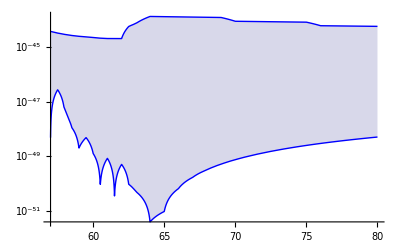

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[ms21[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[ms21[[All,{1,2}]],First]
fis2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fis22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];

me2=(First[SortBy[#1,Last]]&)/@SplitBy[ms12[[All,{1,2}]],First]
me22=(Last[SortBy[#1,Last]]&)/@SplitBy[ms12[[All,{1,2}]],First]
mis2=Interpolation[me2[[All,{1,2}]],InterpolationOrder->1];
mis22=Interpolation[me22[[All,{1,2}]],InterpolationOrder->1];

ne2=(First[SortBy[#1,Last]]&)/@SplitBy[ms22[[All,{1,2}]],First]
ne22=(Last[SortBy[#1,Last]]&)/@SplitBy[ms22[[All,{1,2}]],First]
nis2=Interpolation[ne2[[All,{1,2}]],InterpolationOrder->1];
nis22=Interpolation[ne22[[All,{1,2}]],InterpolationOrder->1];

oe2=(First[SortBy[#1,Last]]&)/@SplitBy[msz1[[All,{1,2}]],First]
oe22=(Last[SortBy[#1,Last]]&)/@SplitBy[msz1[[All,{1,2}]],First]
ois2=Interpolation[oe2[[All,{1,2}]],InterpolationOrder->1];
ois22=Interpolation[oe22[[All,{1,2}]],InterpolationOrder->1];

pe2=(First[SortBy[#1,Last]]&)/@SplitBy[msz2[[All,{1,2}]],First]
pe22=(Last[SortBy[#1,Last]]&)/@SplitBy[msz2[[All,{1,2}]],First]
pis2=Interpolation[pe2[[All,{1,2}]],InterpolationOrder->1];
pis22=Interpolation[pe22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,80},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

```mathematica
tickSpecification=Table[{10^-(i),Superscript[10,-i]},{i,44,48}];
```

InterpolatingFunction::dmval: Input value {-10.6921} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {393.068} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-10.6921} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

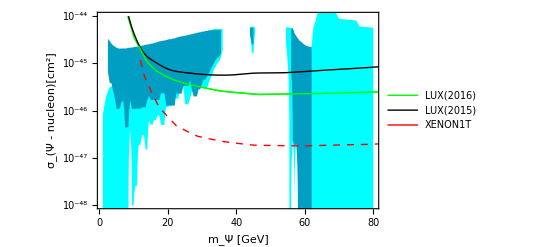

```mathematica
figsignocoh2=Show[LogPlot[σlux16[m],{m,1,100},PlotStyle->{Green},PlotRange->{{1,80},{10^-48,10^-44}}],
LogPlot[{Fb1[m],Fb2[m]},{m,1,36},PlotStyle->{None,None},Filling->{1->{2}},FillingStyle->{Cyan}],
LogPlot[{fis2[m],fis22[m]},{m,54.5,80},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->{Cyan}],
LogPlot[{mis2[m],mis22[m]},{m,2.5,35.5},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->{RGBColor[0,0.62,0.76]}],
LogPlot[{nis2[m],nis22[m]},{m,56,62},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->{RGBColor[0,0.62,0.76]}],
LogPlot[{ois2[m],ois22[m]},{m,44,45.5},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->{Cyan}],
LogPlot[{pis2[m],pis22[m]},{m,44,45},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->{RGBColor[0,0.62,0.76]}],
LogPlot[lux15[m],{m,1,100},PlotStyle->{Black},PlotRange->{10^-48,10^-44},PlotLegends->Placed[LineLegend[{Black},{"LUX(2015)"},LabelStyle->16],{0.58,.22}]],
LogPlot[σlux16[m],{m,1,100},PlotStyle->{Green},PlotLegends->Placed[LineLegend[{Green},{"LUX(2016)"},LabelStyle->16],{0.58,.15}]],
LogPlot[xenon1t[m],{m,1,100},PlotStyle->{Red,Dashed},PlotLegends->Placed[LineLegend[{Red,Dashed},{"XENON1T "},LabelStyle->16],{0.58,.08}]],
(*LogPlot[Atlas[m],{m,4,63.5},PlotRange->{10.^-48,10.^-43},PlotStyle->{Red, Dashed},Frame->{True,True,False,False},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ψ\)]\) (GeV)","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)(\!\(\*SuperscriptBox[\(cm\), \(2\)]\))"},PlotLegends->Placed[LineLegend[{Red},{"Atlas 90% C.L. (2015)"},LabelStyle->12],{0.655,.77}]]*)Frame->True,FrameLabel->{"m_Ψ [GeV]","\!\(\*SubscriptBox[\(σ\), \(Ψ - nucleon\)]\)[\!\(\*SuperscriptBox[\(cm\), \(2\)]\)]"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
figsignocoh=Show[ListLogPlot[{Table[{om1[[i,1]],om1[[i,10]]},{i,1,Length[om1]}],Table[{om1d[[i,1]],om1d[[i,10]]},{i,1,Length[om1d]}],Table[{om2[[i,1]],om2[[i,10]]},{i,1,Length[om2]}],Table[{om2d[[i,1]],om2d[[i,10]]},{i,1,Length[om2d]}],Table[{omz[[i,1]],omz[[i,10]]},{i,1,Length[omz]}],Table[{omzd[[i,1]],omzd[[i,10]]},{i,1,Length[omzd]}]},PlotRange->{{1,80},{10^-48,10^-44}},PlotStyle->{RGBColor[0,0.62,0.76],Cyan,RGBColor[0,0.62,0.76],Cyan,RGBColor[0,0.62,0.76],Cyan},PlotStyle->PointSize[Tiny]],
LogPlot[σlux16[m],{m,1,80},PlotStyle->{Green},PlotLegends->Placed[LineLegend[{Green},{"Lux 90% C.L. (2016)"},LabelStyle->16],{0.68,.52}]],
LogPlot[lux15[m],{m,4,80},PlotStyle->{Black},PlotRange->{10^-48,10^-44},PlotLegends->Placed[LineLegend[{Black},{"Lux 90% C.L. (2015)"},LabelStyle->16],{0.68,.52}]],
LogPlot[xenon1t[m],{m,7,80},PlotStyle->{Red,Dashed},PlotRange->{10^-48,10^-44},PlotLegends->Placed[LineLegend[{Red,Dashed},{"Xenon1T"},LabelStyle->16],{0.68,.52}]],
(*LogPlot[Atlas[m],{m,4,63.5},PlotRange->{10.^-48,10.^-43},PlotStyle->{Red, Dashed},Frame->{True,True,False,False},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ψ\)]\) (GeV)","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)(\!\(\*SuperscriptBox[\(cm\), \(2\)]\))"},PlotLegends->Placed[LineLegend[{Red},{"Atlas 90% C.L. (2015)"},LabelStyle->12],{0.655,.77}]]*)Frame->True,FrameLabel->{"m_Ψ [GeV]","σ_(Ψ - nucleon)[cm^2]"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

InterpolatingFunction::dmval: Input value {-10.7131} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Export["DDincoherentLux16.png",figsignocoh2]
Export["DDincoherentLux16.pdf",figsignocoh2]
```

DDincoherentLux16.png

DDincoherentLux16.pdf

```mathematica
ptsAbLuxND[[2]]
```

{2.5,9.8076×10^-46}

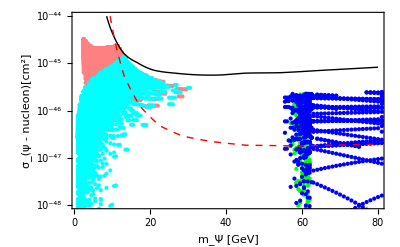

```mathematica
figsignocoh2=Show[ListLogPlot[{Table[{ptsAbLuxND[[i,1]],ptsAbLuxND[[i,10]]},{i,1,Length[ptsAbLuxND]}],Table[{ptsAbLuxND2[[i,1]],ptsAbLuxND2[[i,10]]},{i,1,Length[ptsAbLuxND2]}],Table[{ptsAbLuxD[[i,1]],ptsAbLuxD[[i,10]]},{i,1,Length[ptsAbLuxD]}],Table[{ptsAbLuxD2[[i,1]],ptsAbLuxD2[[i,10]]},{i,1,Length[ptsAbLuxD2]}]},PlotRange->{{1,80},{10^-48,10^-44}},PlotStyle->{Pink,Green,Cyan,Blue},PlotStyle->PointSize[Tiny]],
LogPlot[lux15[m],{m,4,80},PlotStyle->{Black},PlotRange->{10^-48,10^-44},PlotLegends->Placed[LineLegend[{Black},{"Lux 90% C.L. (2015)"},LabelStyle->16],{0.68,.52}]],
LogPlot[xenon1t[m],{m,7,80},PlotStyle->{Red,Dashed},PlotRange->{10^-48,10^-44},PlotLegends->Placed[LineLegend[{Red,Dashed},{"Xenon1T"},LabelStyle->16],{0.68,.52}]],
(*LogPlot[Atlas[m],{m,4,63.5},PlotRange->{10.^-48,10.^-43},PlotStyle->{Red, Dashed},Frame->{True,True,False,False},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ψ\)]\) (GeV)","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)(\!\(\*SuperscriptBox[\(cm\), \(2\)]\))"},PlotLegends->Placed[LineLegend[{Red},{"Atlas 90% C.L. (2015)"},LabelStyle->12],{0.655,.77}]]*)Frame->True,FrameLabel->{"m_Ψ [GeV]","\!\(\*SubscriptBox[\(σ\), \(ψ - nucleon\)]\)[\!\(\*SuperscriptBox[\(cm\), \(2\)]\)]"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["DDincoherent.png",figsignocoh2]
```

DDincoherent.png

```mathematica
Export["DD_PlanckLux15_ND1.dat",ptsAbLuxND]
```

DD_PlanckLux15_ND1.dat

```mathematica
Export["DD_PlanckLux15_ND2.dat",ptsAbLuxND2]
```

DD_PlanckLux15_ND2.dat

```mathematica
Export["DD_PlanckLux15_D1.dat",ptsAbLuxD]
```

DD_PlanckLux15_D1.dat

```mathematica
Export["DD_PlanckLux15_D2.dat",ptsAbLuxD2]
```

DD_PlanckLux15_D2.dat

List in order : Mpsi,  Lam,  mu (1), mu (3), Lx, kk, Om, SigmaPsiP, SigmaPsiN, SigTotIncoh, NuFlux from Sun, MuonFlux Upward, MuonFlux Contained, Z width, H width, HBR inv

Indirect Detection

```mathematica
vev=246.;
MH=125.7;
MZ=91.1876;
MW=80.401;
GZ=2.49;
GH=.004;
mτ=1.77682;
MTA=mτ;
mt=173.21;
MB=4.66;
(*cviiR=-10.;
cviiL=-8;*)
cw=MW/MZ;
gew=2*MW/vev;
gLmRb=-1+4/3 (cw^2-1);
gzz=gew/(4 Pi cw);
(*ciii=1.5;
cii=.1;*)
w=ArcCos[80.385/91.1876];
```

```mathematica
gevI2cm2=0.3894*10^(-27)2.9979*10^10;
```

```mathematica
svnn[mpsi_,mudm1_,mphi_,Lam_]:=gevI2cm2 2^4 mpsi^2 mudm1^4/(64 (mphi^2+mpsi^2)^2 Pi Lam^4 )
```

```mathematica
svnn2[mpsi_,etasq_,mphi_]:=gevI2cm2 2^4 mpsi^2 etasq^2/(64 (mphi^2+mpsi^2)^2 Pi )
```

```mathematica
Solve[svnn2[.1,x,(10+.1)*1]==3*10^-26,x]
```

{{x→-0.183335},{x→0.183335}}

```mathematica
Solve[svnn[1,.001*x^2,11,x]==3.*10^-26,x]
```

{{x→-148.067},{x→0.-148.067 ⅈ},{x→0.+148.067 ⅈ},{x→148.067}}

```mathematica
(gz^4 Sqrt[1-MB^2/mpsi^2] mpsi^2 Nf zi2di2^2 (1/4 (1+gLmGr^2+((-3+gLmGr^2) MB^2)/(2 mpsi^2)) Log[Λ/mphi]+(1/8 (1+gLmGr^2)+((-1+gLmGr^2) MB^2)/(16 mpsi^2)) (1+Log[Λ/mphi]^2)))/(64 (16 mpsi^4+Gz^2 MZ^2-8 mpsi^2 MZ^2+MZ^4) π )
```

(gz^4 √(1-21.7156/mpsi^2) mpsi^2 Nf zi2di2^2 (1/4 (1+gLmGr^2+(10.8578 (-3+gLmGr^2))/mpsi^2) Log[Λ/mphi]+(1/8 (1+gLmGr^2)+(1.35723 (-1+gLmGr^2))/mpsi^2) (1+Log[Λ/mphi]^2)))/(64 (6.91422×10^7+8315.18 Gz^2-66521.4 mpsi^2+16 mpsi^4) π)

```mathematica
svffZ[mpsi_,Lam_,mu3_,mphi_,z_,MB_,gLmGr_,Nf_]:=gevI2cm2(gzz^4 Sqrt[1-MB^2/mpsi^2] mpsi^2 Nf (z*mu3/Lam)^4 (1/4 (1+gLmGr^2+((-3+gLmGr^2) MB^2)/(2 mpsi^2)) Log[Lam/mphi]+(1/8 (1+gLmGr^2)+(-1+gLmGr^2) MB^2 (1+Log[Lam/mphi]^2))/(8 mpsi^2)))/(64 (16 mpsi^4+GZ^2 MZ^2-8 mpsi^2 MZ^2+MZ^4) π)
```

```mathematica
svnn[mpsi,118,10+mpsi,1000]
```

(1.80107×10^-22 mpsi^2)/((mpsi^2+(10+mpsi)^2)^2)

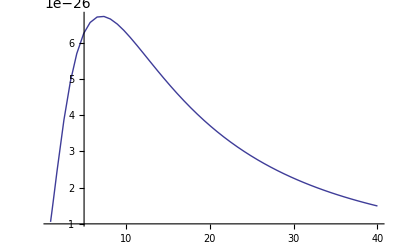

```mathematica
Plot[svnn[mpsi,114,10+mpsi,1000],{mpsi,1,40}]
```

InterpolatingFunction::dmval: Input value {620.378} lies outside the range of data in the interpolating function. Extrapolation will be used.

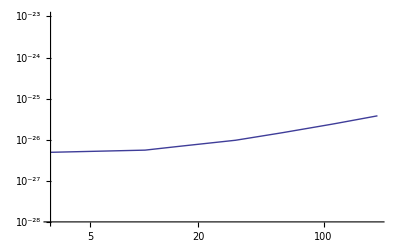

```mathematica
Get["/media/vanniagm/36887AD4887A925B/nu_portal/MATH_NUMODEL/fermilat.m"]
```

```mathematica
svbb[mpsi_,mudm3_,Lx_,Lam_,mphi_,z3_]:=(.001)^2*gevI2cm2(-3 (MB^2 (MB-mpsi) (MB+mpsi)Sqrt[1-MB^2/mpsi^2] (z3^2*mudm3^2+Lx vev^2 z3^2 Log[Lam/mphi])^2))/(256 ((GH^2 MH^2+(MH^2-4 mpsi^2)^2) Pi π^4 vev^4 Lam^2))
```

```mathematica
omnd1=ptsAbLuxND;omnd2=ptsAbLuxND2;
omnd[[1]]
```

{2.5,1685.,193.9,193.9,-0.6,1.,0.12698,2.7531×10^-45,1.8438×10^-46,6.3725×10^-46,1.3421×10^8,0.0004778,0.12806,2.4014,0.0075156,0.1951}

```mathematica
omd1=ptsAbLuxD;omd2=ptsAbLuxD2;
```

```mathematica
omd1[[1]]
```

{1.,497.,12.12,12.12,0.,0.09182,0.11712,5.9331×10^-48,1.7775×10^-50,1.8955×10^-48,0.,0.,0.,2.4097,0.0060496,3.041×10^-6}

```mathematica
Listsvnn1=Table[{omnd1[[i,1]],svnn[omnd1[[i,1]],omnd1[[i,3]],(10+omnd1[[i,1]])*omnd1[[i,6]],omnd1[[i,2]]]},{i,1,Length[omnd1]}];
Listsvnn22=Table[{omnd2[[i,1]],svnn[omnd2[[i,1]],omnd2[[i,3]],(10+omnd2[[i,1]])*omnd2[[i,6]],omnd2[[i,2]]]},{i,1,Length[omnd2]}];
Listsvnn2=Table[If[Listsvnn22[[i,2]]>=10^-40,{Listsvnn22[[i,1]],Listsvnn22[[i,2]]},Unevaluated[Sequence[]]],{i,1,Length[Listsvnn22]}];
Listsvnnd1=Table[{omd1[[i,1]],svnn[omd1[[i,1]],omd1[[i,3]],(10+omd1[[i,1]])*omd[[i,6]],omd1[[i,2]]]},{i,1,Length[omd1]}];
Listsvnnd22=Table[{omd2[[i,1]],svnn[omd2[[i,1]],omd2[[i,3]],(10+omd2[[i,1]])*omd2[[i,6]],omd2[[i,2]]]},{i,1,Length[omd2]}];
Listsvnnd2=Table[If[Listsvnnd22[[i,2]]>=10^-40,{Listsvnnd22[[i,1]],Listsvnnd22[[i,2]]},Unevaluated[Sequence[]]],{i,1,Length[Listsvnnd22]}];
```

```mathematica
Listsvff1=Table[If[omnd1[[i,1]]>MB,{omnd1[[i,1]],svffZ[omnd1[[i,1]],omnd1[[i,2]],omnd1[[i,4]],(10+omnd1[[i,1]])*omnd1[[i,6]],2,MB,gLmRb,3]},Unevaluated[Sequence[]]],{i,1,Length[omnd1]}];
Listsvff22=Table[If[omnd2[[i,1]]>MB,{omnd2[[i,1]],svffZ[omnd2[[i,1]],omnd2[[i,2]],omnd2[[i,4]],(10+omnd2[[i,1]])*omnd2[[i,6]],2,MB,gLmRb,3]},Unevaluated[Sequence[]]],{i,1,Length[omnd2]}];Listsvff2=Table[If[Listsvff22[[i,2]]>0,{Listsvff22[[i,1]],Listsvff22[[i,2]]},Unevaluated[Sequence[]]],{i,1,Length[Listsvff22]}];
Listsvffd1=Table[If[omd1[[i,1]]>MB,{omd1[[i,1]],svffZ[omd1[[i,1]],omd1[[i,2]],omd1[[i,4]],(10+omd1[[i,1]])*omd1[[i,6]],2,MB,gLmRb,3]},Unevaluated[Sequence[]]],{i,1,Length[omd1]}];
Listsvffd22=Table[If[omd2[[i,1]]>MB,{omd2[[i,1]],svffZ[omd2[[i,1]],omd2[[i,2]],omd2[[i,4]],(10+omd2[[i,1]])*omd2[[i,6]],2,MB,gLmRb,3]},Unevaluated[Sequence[]]],{i,1,Length[omd2]}];
Listsvffd2=Table[If[Listsvffd22[[i,2]]>=10^-40,{Listsvffd22[[i,1]],Listsvffd22[[i,2]]},Unevaluated[Sequence[]]],{i,1,Length[Listsvffd22]}];
```

```mathematica
Listsvffd2log=Table[If[Listsvffd22[[i,2]]>=10^-40,{Listsvffd22[[i,1]],Log[Listsvffd22[[i,2]]]},Unevaluated[Sequence[]]],{i,1,Length[Listsvffd22]}];
```

```mathematica
Listsvbb=Table[{om[[i,1]],svbb[om[[i,1]],om[[i,4]],om[[i,5]],om[[i,2]],(10+om[[i,1]])*om[[i,6]],2]},{i,1,Length[om]}];
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvff1[[All,{1,2}]],First]
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvff1[[All,{1,2}]],First]
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->2];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->2];
Lbb1=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvff2[[All,{1,2}]],First]
Lbb2=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvff2[[All,{1,2}]],First]
Fbb1=Interpolation[Lbb1[[All,{1,2}]],InterpolationOrder->2];
Fbb2=Interpolation[Lbb2[[All,{1,2}]],InterpolationOrder->2];
```

{{5.,8.20232×10^-34},{5.5,1.40511×10^-33},{6.,1.93023×10^-33},{6.5,3.05497×10^-33},{7.,3.71191×10^-33},{7.5,3.56733×10^-33},{8.,4.1601×10^-33},{8.5,4.78723×10^-33},{9.,6.6638×10^-33},{9.5,7.56677×10^-33},{10.,8.48176×10^-33},{10.5,9.45227×10^-33},{11.,8.53853×10^-33},{11.5,9.42362×10^-33},{12.,1.03594×10^-32},{12.5,1.13484×10^-32},{13.,1.23937×10^-32},{13.5,1.34985×10^-32},{14.,2.26446×10^-32},{14.5,2.42344×10^-32},{15.,2.62504×10^-32},{15.5,2.83867×10^-32},{16.,3.06511×10^-32},{16.5,3.04239×10^-32},{17.,3.2744×10^-32},{17.5,3.52039×10^-32},{18.,3.78138×10^-32},{18.5,4.05847×10^-32},{19.,6.15312×10^-32},{19.5,5.87325×10^-32},{20.,6.2946×10^-32},{20.5,6.74365×10^-32},{21.,7.2227×10^-32},{21.5,7.7343×10^-32},{22.,8.28129×10^-32},{22.5,1.04809×10^-31},{23.,1.12253×10^-31},{23.5,1.20245×10^-31},{24.,1.28836×10^-31},{24.5,1.56896×10^-31},{25.,1.6826×10^-31},{25.5,1.80537×10^-31},{26.,1.93824×10^-31},{27.,2.8873×10^-31},{27.5,2.9016×10^-31},{28.,3.12629×10^-31},{28.5,3.37204×10^-31},{29.,3.90195×10^-31},{29.5,4.21977×10^-31}}

{{5.,2.36685×10^-33},{5.5,3.68403×10^-33},{6.,4.68778×10^-33},{6.5,5.72236×10^-33},{7.,6.66148×10^-33},{7.5,7.74491×10^-33},{8.,8.90821×10^-33},{8.5,1.01847×10^-32},{9.,1.17286×10^-32},{9.5,1.32732×10^-32},{10.,1.50792×10^-32},{10.5,1.70351×10^-32},{11.,1.91599×10^-32},{11.5,2.17704×10^-32},{12.,2.41283×10^-32},{12.5,2.61678×10^-32},{13.,2.83744×10^-32},{13.5,3.02767×10^-32},{14.,3.24131×10^-32},{14.5,3.48959×10^-32},{15.,3.85985×10^-32},{15.5,4.16339×10^-32},{16.,4.48627×10^-32},{16.5,4.84127×10^-32},{17.,5.21787×10^-32},{17.5,5.65739×10^-32},{18.,6.08553×10^-32},{18.5,6.89998×10^-32},{19.,7.41182×10^-32},{19.5,7.6549×10^-32},{20.,8.73469×10^-32},{20.5,9.36868×10^-32},{21.,1.0046×10^-31},{21.5,1.07703×10^-31},{22.,1.21048×10^-31},{22.5,1.29736×10^-31},{23.,1.48033×10^-31},{23.5,1.58705×10^-31},{24.,1.59852×10^-31},{24.5,1.71463×10^-31},{25.,1.6826×10^-31},{25.5,1.80537×10^-31},{26.,1.93824×10^-31},{27.,2.8873×10^-31},{27.5,3.10817×10^-31},{28.,3.3492×10^-31},{28.5,3.61285×10^-31},{29.,3.90195×10^-31},{29.5,4.21977×10^-31}}

{{56.5,6.59648×10^-31},{57.,1.01091×10^-31},{57.5,3.35087×10^-32},{58.,1.21268×10^-34},{58.5,3.62948×10^-35},{59.,1.41644×10^-35},{59.5,5.57197×10^-36},{60.,2.27512×10^-36},{60.5,1.20131×10^-36},{61.,6.85763×10^-37},{61.5,5.38623×10^-37},{62.,7.40602×10^-37},{84.,4.09611×10^-33}}

{{56.5,6.59648×10^-31},{57.,9.37342×10^-31},{57.5,1.21557×10^-30},{58.,8.83626×10^-31},{58.5,6.83891×10^-31},{59.,6.9125×10^-31},{59.5,4.61903×10^-31},{60.,4.55225×10^-31},{60.5,4.98282×10^-31},{61.,3.85641×10^-31},{61.5,3.6518×10^-31},{62.,3.43499×10^-31},{84.,4.09611×10^-33}}

{{5.,1.03905×10^-34},{5.5,2.60088×10^-34},{6.,3.36301×10^-34},{6.5,5.17779×10^-34},{7.,7.14264×10^-34},{7.5,1.00041×10^-33},{8.,1.3466×10^-33},{8.5,9.53585×10^-34},{9.,2.57352×10^-33},{9.5,2.8214×10^-33},{10.,3.14041×10^-33},{10.5,3.49817×10^-33},{11.,3.99477×10^-33},{11.5,4.59107×10^-33},{12.,6.26743×10^-33},{12.5,6.04106×10^-33},{13.,6.56952×10^-33},{13.5,9.61448×10^-33},{14.,1.04161×10^-32},{14.5,1.31459×10^-32},{15.,1.41976×10^-32},{15.5,1.23972×10^-32},{16.,1.33185×10^-32},{16.5,1.80551×10^-32},{17.,2.78535×10^-32},{17.5,2.92388×10^-32},{18.,3.07965×10^-32},{18.5,3.29955×10^-32},{19.,3.53309×10^-32},{19.5,4.6076×10^-32},{20.,4.0881×10^-32},{20.5,4.36723×10^-32},{21.,4.66477×10^-32},{21.5,7.48464×10^-32},{22.,8.00551×10^-32},{22.5,8.56319×10^-32},{23.,1.05625×10^-31},{23.5,1.13034×10^-31},{24.,1.21001×10^-31},{24.5,1.5621×10^-31},{25.,1.39703×10^-31},{25.5,1.49631×10^-31},{26.,1.60371×10^-31},{26.5,2.0263×10^-31},{27.,2.17564×10^-31},{27.5,2.33801×10^-31},{28.,2.51516×10^-31},{30.,4.95791×10^-31},{30.5,5.37341×10^-31}}

{{5.,2.1999×10^-34},{5.5,4.21936×10^-34},{6.,6.37798×10^-34},{6.5,8.97111×10^-34},{7.,1.21614×10^-33},{7.5,1.58559×10^-33},{8.,2.05013×10^-33},{8.5,2.52232×10^-33},{9.,3.19456×10^-33},{9.5,4.00683×10^-33},{10.,4.85017×10^-33},{10.5,5.93193×10^-33},{11.,7.06779×10^-33},{11.5,8.53672×10^-33},{12.,1.00103×10^-32},{12.5,1.18079×10^-32},{13.,1.39642×10^-32},{13.5,1.61763×10^-32},{14.,1.87385×10^-32},{14.5,2.12313×10^-32},{15.,2.37427×10^-32},{15.5,2.68953×10^-32},{16.,2.93248×10^-32},{16.5,3.23644×10^-32},{17.,3.57027×10^-32},{17.5,4.0019×10^-32},{18.,4.53081×10^-32},{18.5,4.94047×10^-32},{19.,5.61903×10^-32},{19.5,6.12713×10^-32},{20.,6.73071×10^-32},{20.5,7.66658×10^-32},{21.,7.97033×10^-32},{21.5,9.13882×10^-32},{22.,9.78441×10^-32},{22.5,1.10206×10^-31},{23.,1.17997×10^-31},{23.5,1.3612×10^-31},{24.,1.45793×10^-31},{24.5,1.5621×10^-31},{25.,1.71769×10^-31},{25.5,1.84164×10^-31},{26.,2.14474×10^-31},{26.5,2.4784×10^-31},{27.,2.6635×10^-31},{27.5,2.33801×10^-31},{28.,2.51516×10^-31},{30.,4.95791×10^-31},{30.5,5.37341×10^-31}}

InterpolatingFunction::dmval: Input value {57.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

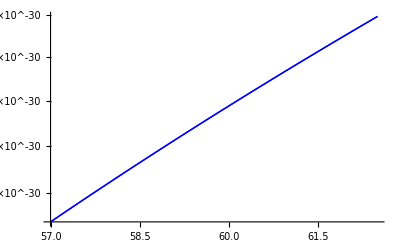

{{55.5,-69.606},{56.,-71.7779},{56.5,-71.8704},{57.,-70.6565},{57.5,-71.3836},{58.,-72.4919},{58.5,-74.9966},{59.,-78.7994},{59.5,-79.6317},{60.,-80.5228},{60.5,-81.2636},{61.,-81.8994},{61.5,-82.2161},{62.,-82.1465},{62.5,-71.2779},{63.,-70.0588},{64.,-70.7939},{65.,-70.8953},{66.,-70.9916},{67.,-71.0834},{68.,-71.1711},{69.,-71.255},{70.,-70.9523},{71.,-71.0286},{72.,-71.1021},{73.,-71.1729},{74.,-71.2413},{75.,-71.3073},{76.,-71.1118},{77.,-71.173},{78.,-71.2324},{79.,-71.2901},{80.,-71.3462},{81.,-77.9664},{82.,-71.2637},{82.5,-76.7082},{83.,-71.315},{84.,-71.5559},{85.,-75.9546},{86.,-71.4612},{87.,-71.5077},{88.,-71.5531},{89.,-71.5975},{90.,-71.6409},{92.,-74.7413},{92.5,-77.4824},{93.,-77.5057},{95.,-71.8454},{100.,-81.9703},{105.,-72.203},{110.,-72.3619},{115.,-72.5103},{120.,-72.6496},{125.,-75.3426},{126.,-76.4959},{127.,-78.4163},{130.,-83.682},{135.,-73.0244},{140.,-74.8066},{145.,-74.921},{150.,-73.3503},{155.,-78.1476},{165.,-74.7626},{170.,-74.8555},{175.,-74.9457},{180.,-73.7251},{185.,-77.3352},{190.,-73.8846},{195.,-74.8745},{200.,-74.9511}}

{{55.5,-68.4804},{56.,-68.5736},{56.5,-68.6623},{57.,-69.0793},{57.5,-68.9859},{58.,-69.2386},{58.5,-69.3131},{59.,-69.5264},{59.5,-69.7103},{60.,-69.8717},{60.5,-69.9148},{61.,-69.9764},{61.5,-70.2017},{62.,-70.2589},{62.5,-69.4853},{63.,-68.9126},{64.,-69.0151},{65.,-69.112},{66.,-69.2039},{67.,-69.2912},{68.,-69.3744},{69.,-69.4539},{70.,-69.53},{71.,-69.6028},{72.,-69.6729},{73.,-69.7402},{74.,-69.8052},{75.,-69.8678},{76.,-69.9282},{77.,-69.9867},{78.,-70.0434},{79.,-70.0983},{80.,-70.1516},{81.,-70.2836},{82.,-70.4446},{82.5,-73.7337},{83.,-70.5855},{84.,-70.932},{85.,-70.9798},{86.,-71.0263},{87.,-71.0718},{88.,-71.1162},{89.,-71.1596},{90.,-71.281},{92.,-72.2706},{92.5,-74.1521},{93.,-72.3122},{95.,-71.5784},{100.,-71.8811},{105.,-72.0508},{110.,-72.3619},{115.,-72.5103},{120.,-72.6496},{125.,-72.7812},{126.,-73.0422},{127.,-75.1874},{130.,-72.9059},{135.,-73.0244},{140.,-73.1378},{145.,-73.2462},{150.,-73.3503},{155.,-73.4261},{165.,-73.4675},{170.,-73.5561},{175.,-73.6419},{180.,-73.7251},{185.,-73.8059},{190.,-73.8846},{195.,-73.9611},{200.,-74.9511}}

InterpolatingFunction[{{55.5,200.}},<>]

InterpolatingFunction[{{55.5,200.}},<>]

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvffd1[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvffd1[[All,{1,2}]],First]
fis2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fis22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
see2=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvffd2log[[All,{1,2}]],First]
see22=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvffd2log[[All,{1,2}]],First]
fise2=Interpolation[Table[{see22[[i,1]],Exp[see22[[i,2]]]},{i,1,Length[see22]}],InterpolationOrder->3]
fise22=Interpolation[Table[{see2[[i,1]],Exp[see2[[i,2]]]},{i,1,Length[see2]}],InterpolationOrder->2]
```

```mathematica
Exp[fise2[60]]
```

1.06997×10^-35

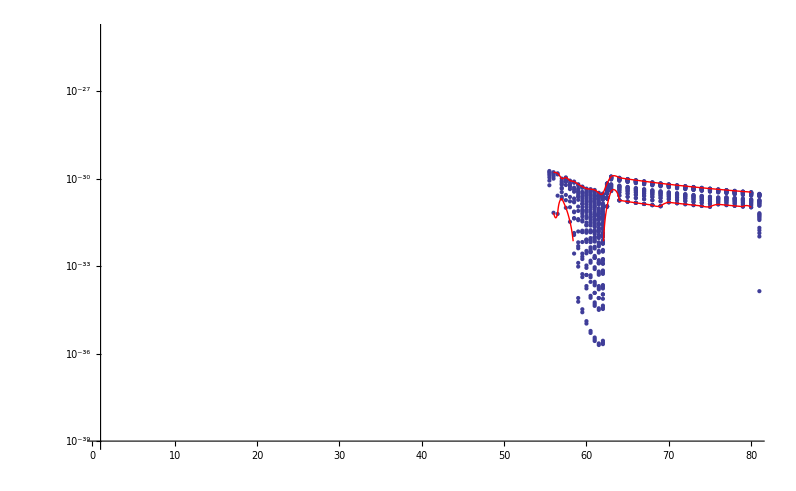

```mathematica
Show[ListLogPlot[Listsvffd2,PlotRange->{{1,80},{10^-39,10^-25}}],LogPlot[{fise2[m],fise22[m]},{m,56,80},PlotStyle->Red,PlotPoints->500]]
```

```mathematica
Table[{see2[[i,1]],Exp[see2[[i,2]]]},{i,1,Length[see2]}]
```

{{55.5,5.89498×10^-31},{56.,6.71843×10^-32},{56.5,6.12438×10^-32},{57.,2.06186×10^-31},{57.5,9.96503×10^-32},{58.,3.28974×10^-32},{58.5,2.68766×10^-33},{59.,5.99615×10^-35},{59.5,2.60859×10^-35},{60.,1.06997×10^-35},{60.5,5.10093×10^-36},{61.,2.70105×10^-36},{61.5,1.96784×10^-36},{62.,2.10977×10^-36},{62.5,1.10768×10^-31},{63.,3.74833×10^-31},{64.,1.79718×10^-31},{65.,1.62394×10^-31},{66.,1.47478×10^-31},{67.,1.34548×10^-31},{68.,1.23255×10^-31},{69.,1.13332×10^-31},{70.,1.53401×10^-31},{71.,1.42124×10^-31},{72.,1.32056×10^-31},{73.,1.23026×10^-31},{74.,1.14895×10^-31},{75.,1.07552×10^-31},{76.,1.30785×10^-31},{77.,1.23013×10^-31},{78.,1.15916×10^-31},{79.,1.09417×10^-31},{80.,1.03451×10^-31},{81.,1.37914×10^-34},{82.,1.12346×10^-31},{82.5,4.8537×10^-34},{83.,1.06733×10^-31},{84.,8.38843×10^-32},{85.,1.03114×10^-33},{86.,9.22127×10^-32},{87.,8.8026×10^-32},{88.,8.41211×10^-32},{89.,8.04643×10^-32},{90.,7.7043×10^-32},{92.,3.46964×10^-33},{92.5,2.23786×10^-34},{93.,2.18634×10^-34},{95.,6.27948×10^-32},{100.,2.51616×10^-36},{105.,4.39159×10^-32},{110.,3.74656×10^-32},{115.,3.2299×10^-32},{120.,2.80979×10^-32},{125.,1.90159×10^-33},{126.,6.00167×10^-34},{127.,8.79459×10^-35},{130.,4.54331×10^-37},{135.,1.93148×10^-32},{140.,3.25022×10^-33},{145.,2.89883×10^-33},{150.,1.39431×10^-32},{155.,1.15065×10^-34},{165.,3.39649×10^-33},{170.,3.09503×10^-33},{175.,2.82802×10^-33},{180.,9.58545×10^-33},{185.,2.59268×10^-34},{190.,8.17221×10^-33},{195.,3.03685×10^-33},{200.,2.81283×10^-33}}

```mathematica
Table[{see22[[i,1]],Exp[see22[[i,2]]]},{i,1,Length[see22]}]
```

{{55.5,1.81691×10^-30},{56.,1.65525×10^-30},{56.5,1.5148×10^-30},{57.,9.98214×10^-31},{57.5,1.09594×10^-30},{58.,8.51287×10^-31},{58.5,7.9014×10^-31},{59.,6.38366×10^-31},{59.5,5.31112×10^-31},{60.,4.51967×10^-31},{60.5,4.32884×10^-31},{61.,4.07031×10^-31},{61.5,3.24919×10^-31},{62.,3.06876×10^-31},{62.5,6.65122×10^-31},{63.,1.17937×10^-30},{64.,1.06444×10^-30},{65.,9.66134×10^-31},{66.,8.81325×10^-31},{67.,8.07633×10^-31},{68.,7.43145×10^-31},{69.,6.86362×10^-31},{70.,6.36101×10^-31},{71.,5.91383×10^-31},{72.,5.5139×10^-31},{73.,5.15467×10^-31},{74.,4.83068×10^-31},{75.,4.53752×10^-31},{76.,4.27118×10^-31},{77.,4.02855×10^-31},{78.,3.80672×10^-31},{79.,3.60333×10^-31},{80.,3.41635×10^-31},{81.,2.99384×10^-31},{82.,2.54855×10^-31},{82.5,9.503×10^-33},{83.,2.21358×10^-31},{84.,1.56532×10^-31},{85.,1.49238×10^-31},{86.,1.42449×10^-31},{87.,1.36117×10^-31},{88.,1.30207×10^-31},{89.,1.24671×10^-31},{90.,1.10422×10^-31},{92.,4.10486×10^-32},{92.5,6.25406×10^-33},{93.,3.93745×10^-32},{95.,8.20164×10^-32},{100.,6.05929×10^-32},{105.,5.11376×10^-32},{110.,3.74656×10^-32},{115.,3.2299×10^-32},{120.,2.80979×10^-32},{125.,2.46347×10^-32},{126.,1.89753×10^-32},{127.,2.2208×10^-33},{130.,2.17465×10^-32},{135.,1.93148×10^-32},{140.,1.72456×10^-32},{145.,1.54738×10^-32},{150.,1.39431×10^-32},{155.,1.29252×10^-32},{165.,1.24008×10^-32},{170.,1.13499×10^-32},{175.,1.0417×10^-32},{180.,9.58545×10^-33},{185.,8.8408×10^-33},{190.,8.17221×10^-33},{195.,7.56995×10^-33},{200.,2.81283×10^-33}}

```mathematica
Exp[-82.]
```

2.4426×10^-36

InterpolatingFunction::dmval: Input value {2.00059} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {56.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

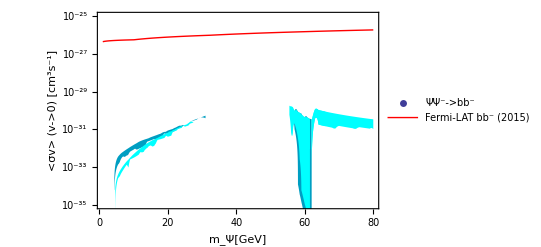

```mathematica
fsvbb=Show[ListLogPlot[{Listsvff2,Listsvff1,Listsvffd2,Listsvffd1},PlotRange->{{1,80},{10^-35,10^-25}},PlotStyle->{None,None,None,None},PlotLegends->Placed[PointLegend[{"ΨΨ^-->bb^-"(*,"ΨΨ^-->H^*->bb^-"*)},LabelStyle->16,LegendFunction->"Frame",Background->White],{0.65,.69}]],
LogPlot[{Fb1[m],Fb2[m]},{m,2,31},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]],
LogPlot[{Fbb1[m],Fbb2[m]},{m,56,62},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]],
LogPlot[{fis2[m],fis22[m]},{m,2,31},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->Cyan],LogPlot[{fise2[m],fise22[m]},{m,55.5,66},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->Cyan],
LogPlot[{fise2[m],fise22[m]},{m,60,80},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->Cyan],
LogPlot[Subscript[Φ,μ][m],{m,1,80},PlotStyle->{Red},PlotLegends->Placed[LineLegend[{Red},{"Fermi-LAT \!\(\*SuperscriptBox[\(bb\), \(-\)]\) (2015)"},LabelStyle->16],{0.65,.87}]],Frame->True,
FrameLabel->{"m_Ψ[GeV]","<σv> (v->0) [\!\(\*SuperscriptBox[\(cm\), \(3\)]\)\!\(\*SuperscriptBox[\(s\), \(-1\)]\)]"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["FermiLux16.png",fsvbb]
```

FermiLux16.png

```mathematica
Export["FermiLux16.pdf",fsvbb]
```

FermiLux16.pdf

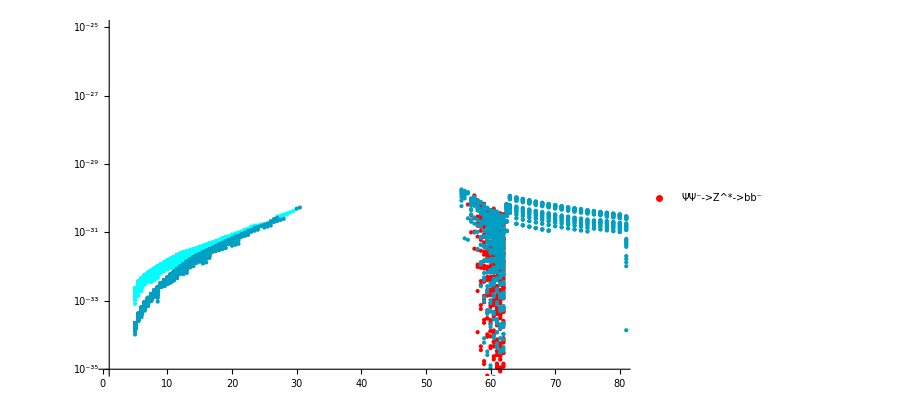

```mathematica
ListLogPlot[{Listsvff2,Listsvff1,Listsvffd2,Listsvffd1},PlotRange->{{1,80},{10^-35,10^-25}},PlotStyle->{Red,Cyan,RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},PlotLegends->Placed[PointLegend[{"ΨΨ^-->Z^*->bb^-"(*,"ΨΨ^-->H^*->bb^-"*)},LabelStyle->16,LegendFunction->"Frame",Background->White],{0.65,.49}]]
```

```mathematica
Export["FermilatLux.pdf",fsvbb]
```

FermilatLux.pdf

InterpolatingFunction::dmval: Input value {464.989} lies outside the range of data in the interpolating function. Extrapolation will be used.

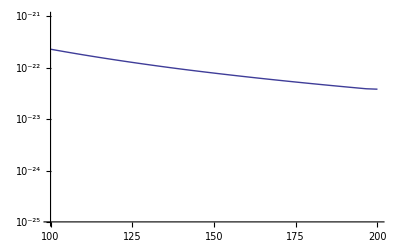

```mathematica
Get["/home/vanniagm/Dropbox/nu_portal/MATH_NUMODEL/icecube.m"]
```

```mathematica
nb1=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvnn1[[All,{1,2}]],First]
nb2=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvnn1[[All,{1,2}]],First]
Fnb1=Interpolation[nb1[[All,{1,2}]],InterpolationOrder->2];
Fnb2=Interpolation[nb2[[All,{1,2}]],InterpolationOrder->2];
nbd1=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvnnd1[[All,{1,2}]],First]
nbd2=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvnnd1[[All,{1,2}]],First]
Fnbd1=Interpolation[nbd1[[All,{1,2}]],InterpolationOrder->2];
Fnbd2=Interpolation[nbd2[[All,{1,2}]],InterpolationOrder->2];
```

{{2.5,3.84011×10^-26},{3.,3.54586×10^-26},{3.5,3.18374×10^-26},{4.,2.89889×10^-26},{4.5,2.70828×10^-26},{5.,2.57738×10^-26},{5.5,2.48011×10^-26},{6.,2.4123×10^-26},{6.5,2.3642×10^-26},{7.,2.32311×10^-26},{7.5,2.29674×10^-26},{8.,2.27179×10^-26},{8.5,2.25298×10^-26},{9.,2.23922×10^-26},{9.5,2.23276×10^-26},{10.,2.2139×10^-26},{10.5,2.20185×10^-26},{11.,2.19766×10^-26},{11.5,2.19609×10^-26},{12.,2.17977×10^-26},{12.5,2.17586×10^-26},{13.,2.16823×10^-26},{13.5,2.16417×10^-26},{14.,2.16265×10^-26},{14.5,2.16891×10^-26},{15.,2.16182×10^-26},{15.5,2.15389×10^-26},{16.,2.13998×10^-26},{16.5,2.14419×10^-26},{17.,2.17694×10^-26},{17.5,2.1438×10^-26},{18.,2.13031×10^-26},{18.5,2.15965×10^-26},{19.,2.12617×10^-26},{19.5,2.17335×10^-26},{20.,2.14382×10^-26},{20.5,2.14053×10^-26},{21.,2.14424×10^-26},{21.5,2.17092×10^-26},{22.,2.11465×10^-26},{22.5,2.20311×10^-26},{23.,2.14689×10^-26},{23.5,2.1955×10^-26},{24.,2.1404×10^-26},{24.5,2.1003×10^-26},{25.,2.21352×10^-26},{25.5,2.1594×10^-26},{26.,2.10708×10^-26},{27.,2.34332×10^-26},{27.5,2.19879×10^-26},{28.,2.14742×10^-26},{28.5,2.0977×10^-26},{29.,2.1328×10^-26},{29.5,2.08433×10^-26}}

{{2.5,4.30212×10^-26},{3.,4.08001×10^-26},{3.5,3.64793×10^-26},{4.,3.32905×10^-26},{4.5,3.10798×10^-26},{5.,2.95473×10^-26},{5.5,2.84832×10^-26},{6.,2.77109×10^-26},{6.5,2.7139×10^-26},{7.,2.66711×10^-26},{7.5,2.63328×10^-26},{8.,2.60651×10^-26},{8.5,2.5825×10^-26},{9.,2.56506×10^-26},{9.5,2.54835×10^-26},{10.,2.53859×10^-26},{10.5,2.52421×10^-26},{11.,2.51436×10^-26},{11.5,2.50747×10^-26},{12.,2.49867×10^-26},{12.5,2.49382×10^-26},{13.,2.48598×10^-26},{13.5,2.4663×10^-26},{14.,2.47283×10^-26},{14.5,2.43981×10^-26},{15.,2.46099×10^-26},{15.5,2.44553×10^-26},{16.,2.42795×10^-26},{16.5,2.4425×10^-26},{17.,2.37592×10^-26},{17.5,2.42463×10^-26},{18.,2.39046×10^-26},{18.5,2.39415×10^-26},{19.,2.38797×10^-26},{19.5,2.416×10^-26},{20.,2.37122×10^-26},{20.5,2.30844×10^-26},{21.,2.38372×10^-26},{21.5,2.32146×10^-26},{22.,2.38748×10^-26},{22.5,2.32607×10^-26},{23.,2.36855×10^-26},{23.5,2.38733×10^-26},{24.,2.32742×10^-26},{24.5,2.2695×10^-26},{25.,2.21352×10^-26},{25.5,2.1594×10^-26},{26.,2.10708×10^-26},{27.,2.34332×10^-26},{27.5,2.28806×10^-26},{28.,2.2346×10^-26},{28.5,2.18287×10^-26},{29.,2.1328×10^-26},{29.5,2.08433×10^-26}}

{{1.,7.40044×10^-26},{1.5,7.18949×10^-26},{2.,7.02373×10^-26},{2.5,6.78756×10^-26},{3.,6.33133×10^-26},{3.5,5.76231×10^-26},{4.,5.28942×10^-26},{4.5,4.94766×10^-26},{5.,4.70609×10^-26},{5.5,4.52628×10^-26},{6.,4.39056×10^-26},{6.5,4.28409×10^-26},{7.,4.19985×10^-26},{7.5,4.12173×10^-26},{8.,4.0666×10^-26},{8.5,4.01655×10^-26},{9.,4.10513×10^-26},{9.5,3.93191×10^-26},{10.,3.90426×10^-26},{10.5,3.87084×10^-26},{11.,3.84656×10^-26},{11.5,3.82432×10^-26},{12.,3.82669×10^-26},{12.5,3.77863×10^-26},{13.,3.75911×10^-26},{13.5,3.73785×10^-26},{14.,3.72266×10^-26},{14.5,3.70125×10^-26},{15.,3.691×10^-26},{15.5,3.67665×10^-26},{16.,3.66691×10^-26},{16.5,3.66025×10^-26},{17.,3.63575×10^-26},{17.5,3.62689×10^-26},{18.,3.61684×10^-26},{18.5,3.639×10^-26},{19.,3.64981×10^-26},{19.5,3.58227×10^-26},{20.,3.63608×10^-26},{20.5,3.57285×10^-26},{21.,3.59562×10^-26},{21.5,3.71158×10^-26},{22.,3.5449×10^-26},{22.5,3.59267×10^-26},{23.,3.5237×10^-26},{23.5,3.58183×10^-26},{24.,3.61047×10^-26},{24.5,3.69823×10^-26},{25.,3.5516×10^-26},{25.5,3.74421×10^-26},{26.,3.6021×10^-26},{26.5,3.48798×10^-26},{27.,3.57167×10^-26},{27.5,3.61175×10^-26},{28.,3.48433×10^-26},{30.,3.85236×10^-26},{30.5,3.72726×10^-26}}

{{1.,8.18943×10^-26},{1.5,8.17987×10^-26},{2.,8.04786×10^-26},{2.5,7.73424×10^-26},{3.,7.01663×10^-26},{3.5,6.61701×10^-26},{4.,6.0738×10^-26},{4.5,5.67342×10^-26},{5.,5.39402×10^-26},{5.5,5.1916×10^-26},{6.,5.02705×10^-26},{6.5,4.90368×10^-26},{7.,4.80472×10^-26},{7.5,4.71617×10^-26},{8.,4.65109×10^-26},{8.5,4.42391×10^-26},{9.,4.54741×10^-26},{9.5,4.50607×10^-26},{10.,4.46223×10^-26},{10.5,4.41967×10^-26},{11.,4.40613×10^-26},{11.5,4.37542×10^-26},{12.,4.34811×10^-26},{12.5,4.3256×10^-26},{13.,4.29792×10^-26},{13.5,4.28227×10^-26},{14.,4.25266×10^-26},{14.5,4.23842×10^-26},{15.,4.22532×10^-26},{15.5,4.20459×10^-26},{16.,4.17594×10^-26},{16.5,4.17208×10^-26},{17.,4.1279×10^-26},{17.5,4.13719×10^-26},{18.,4.09872×10^-26},{18.5,4.09583×10^-26},{19.,4.08958×10^-26},{19.5,4.037×10^-26},{20.,4.03471×10^-26},{20.5,4.04725×10^-26},{21.,4.03468×10^-26},{21.5,4.03166×10^-26},{22.,4.00077×10^-26},{22.5,3.90756×10^-26},{23.,3.94511×10^-26},{23.5,4.01923×10^-26},{24.,3.85388×10^-26},{24.5,3.69823×10^-26},{25.,3.91954×10^-26},{25.5,3.76696×10^-26},{26.,3.85188×10^-26},{26.5,3.91422×10^-26},{27.,3.771×10^-26},{27.5,3.61175×10^-26},{28.,3.48433×10^-26},{30.,3.85236×10^-26},{30.5,3.72726×10^-26}}

```mathematica
sen2=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvnn2[[All,{1,2}]],First]
sen22=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvnn2[[All,{1,2}]],First]
fisn2=Interpolation[sen2[[All,{1,2}]],InterpolationOrder->1];
fisn22=Interpolation[sen22[[All,{1,2}]],InterpolationOrder->1];
send2=(First[SortBy[#1,Last]]&)/@SplitBy[Listsvnnd2[[All,{1,2}]],First]
send22=(Last[SortBy[#1,Last]]&)/@SplitBy[Listsvnnd2[[All,{1,2}]],First]
fisnd2=Interpolation[send2[[All,{1,2}]],InterpolationOrder->1];
fisnd22=Interpolation[send22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fis2[m],fis22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

{{56.5,4.63065×10^-27},{57.,6.98242×10^-28},{57.5,2.186×10^-28},{58.,7.45924×10^-31},{58.5,2.13088×10^-31},{59.,8.17055×10^-32},{59.5,3.16736×10^-32},{60.,1.28022×10^-32},{60.5,6.81769×10^-33},{61.,3.94284×10^-33},{61.5,3.19998×10^-33},{62.,4.70994×10^-33},{84.,3.50022×10^-28}}

{{56.5,4.63065×10^-27},{57.,6.04868×10^-27},{57.5,7.27185×10^-27},{58.,5.26994×10^-27},{58.5,4.37136×10^-27},{59.,5.71225×10^-27},{59.5,3.30617×10^-27},{60.,3.77454×10^-27},{60.5,4.16985×10^-27},{61.,2.54051×10^-27},{61.5,3.13777×10^-27},{62.,2.73435×10^-27},{84.,3.50022×10^-28}}

{{55.5,5.14797×10^-27},{56.,9.78906×10^-28},{56.5,9.61771×10^-28},{57.,2.00692×10^-27},{57.5,9.53679×10^-28},{58.,2.97717×10^-28},{58.5,2.37224×10^-29},{59.,5.11182×10^-31},{59.5,2.19279×10^-31},{60.,8.8423×10^-32},{60.5,4.19709×10^-32},{61.,2.22961×10^-32},{61.5,1.66481×10^-32},{62.,1.8757×10^-32},{62.5,2.51729×10^-27},{63.,6.13497×10^-27},{64.,3.87146×10^-27},{65.,3.75342×10^-27},{66.,3.64031×10^-27},{67.,3.53266×10^-27},{68.,3.42938×10^-27},{69.,3.33023×10^-27},{70.,4.20568×10^-27},{71.,4.0886×10^-27},{72.,3.976×10^-27},{73.,3.86767×10^-27},{74.,3.76341×10^-27},{75.,3.66384×10^-27},{76.,4.21484×10^-27},{77.,4.10654×10^-27},{78.,4.00209×10^-27},{79.,3.90132×10^-27},{80.,3.80406×10^-27},{81.,1.1608×10^-29},{82.,4.06267×10^-27},{82.5,3.89525×10^-29},{83.,3.96519×10^-27},{84.,3.45021×10^-27},{85.,8.22533×10^-29},{86.,3.69333×10^-27},{87.,3.60879×10^-27},{88.,3.52773×10^-27},{89.,3.44844×10^-27},{90.,3.37239×10^-27},{92.,2.72878×10^-28},{92.5,2.19722×10^-29},{93.,2.17403×10^-29},{95.,3.02681×10^-27},{100.,3.2747×10^-31},{105.,2.47753×10^-27},{110.,2.25771×10^-27},{115.,2.06551×10^-27},{120.,1.897×10^-27},{125.,2.00457×10^-28},{126.,7.075×10^-29},{127.,1.18449×10^-29},{130.,7.4794×10^-32},{135.,1.49898×10^-27},{140.,3.3269×10^-28},{145.,3.1019×10^-28},{150.,1.214×10^-27},{155.,1.66385×10^-29},{165.,3.66051×10^-28},{170.,3.44838×10^-28},{175.,3.25426×10^-28},{180.,9.16844×10^-28},{185.,3.76377×10^-29},{190.,8.228×10^-28},{195.,3.46501×10^-28},{200.,3.29374×10^-28}}

{{55.5,1.08168×10^-26},{56.,1.06238×10^-26},{56.5,1.04378×10^-26},{57.,8.4067×10^-27},{57.5,8.26146×10^-27},{58.,8.11964×10^-27},{58.5,6.09688×10^-27},{59.,5.00498×10^-27},{59.5,5.24319×10^-27},{60.,3.68347×10^-27},{60.5,4.39436×10^-27},{61.,4.32271×10^-27},{61.5,3.08913×10^-27},{62.,2.8386×10^-27},{62.5,8.52932×10^-27},{63.,1.12235×10^-26},{64.,1.08747×10^-26},{65.,1.05431×10^-26},{66.,1.02254×10^-26},{67.,9.92305×10^-27},{68.,9.63293×10^-27},{69.,9.35444×10^-27},{70.,9.08904×10^-27},{71.,8.83599×10^-27},{72.,8.59266×10^-27},{73.,8.35855×10^-27},{74.,8.13322×10^-27},{75.,7.91804×10^-27},{76.,7.71073×10^-27},{77.,7.5126×10^-27},{78.,7.32152×10^-27},{79.,7.13717×10^-27},{80.,6.95924×10^-27},{81.,6.60038×10^-27},{82.,6.17174×10^-27},{82.5,5.79629×10^-28},{83.,5.79443×10^-27},{84.,4.91321×10^-27},{85.,4.79861×10^-27},{86.,4.68775×10^-27},{87.,4.58044×10^-27},{88.,4.47756×10^-27},{89.,4.37693×10^-27},{90.,4.11339×10^-27},{92.,2.15273×10^-27},{92.5,4.49648×10^-28},{93.,2.10697×10^-27},{95.,3.50879×10^-27},{100.,2.97019×10^-27},{105.,2.694×10^-27},{110.,2.25771×10^-27},{115.,2.06551×10^-27},{120.,1.897×10^-27},{125.,1.74819×10^-27},{126.,1.41299×10^-27},{127.,2.30653×10^-28},{130.,1.6162×10^-27},{135.,1.49898×10^-27},{140.,1.39359×10^-27},{145.,1.29934×10^-27},{150.,1.214×10^-27},{155.,1.14782×10^-27},{165.,1.09099×10^-27},{170.,1.02776×10^-27},{175.,9.69908×10^-28},{180.,9.16844×10^-28},{185.,8.67886×10^-28},{190.,8.228×10^-28},{195.,7.81198×10^-28},{200.,3.29374×10^-28}}

InterpolatingFunction::dmval: Input value {57.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

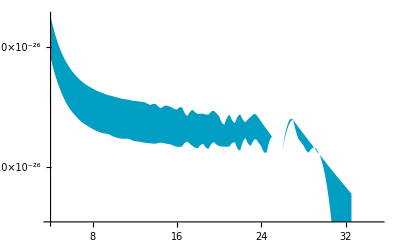

```mathematica
Show[LogPlot[{Fnb1[m],Fnb2[m]},{m,4,35},PlotStyle->{None,None},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],LogPlot[{fisn2[m],fisn22[m]},{m,57,80},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]],
LogPlot[{Fnbd1[m],Fnbd2[m]},{m,4,35},PlotStyle->{None,None},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],LogPlot[{fisnd2[m],fisnd22[m]},{m,57,80},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]]]
```

InterpolatingFunction::dmval: Input value {2.00056} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {54.0002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

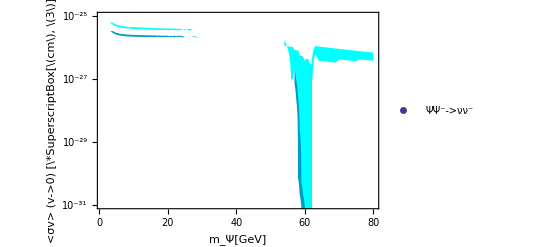

```mathematica
fsvnn=Show[ListLogPlot[{Listsvnn1,Listsvnn2,Listsvnnd1,Listsvnnd2},PlotRange->{{1,80},{10^-31,10^-25}},PlotStyle->{None,None,None,None},PlotLegends->Placed[PointLegend[{"ΨΨ^-->νν^-"},LabelStyle->16,LegendFunction->"Frame",Background->White],{0.25,.75}]],
LogPlot[{Fnb1[m],Fnb2[m]},{m,2,29.5},PlotStyle->{None,None},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],
LogPlot[{Fnbd1[m],Fnbd2[m]},{m,2,30.5},PlotStyle->{None,None},Filling->{1->{2}},FillingStyle->Cyan],
LogPlot[{fisn2[m],fisn22[m]},{m,57,62},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->RGBColor[0,0.62,0.76]],
LogPlot[{fisnd2[m],fisnd22[m]},{m,54,62},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->Cyan],LogPlot[{fisnd2[m],fisnd22[m]},{m,62,80},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->Cyan],
Frame->True,FrameLabel->{"m_Ψ[GeV]","<σv> (v->0) [\*SuperscriptBox[\(cm\), \(3\)]s^-1]"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["SVnnLux16.png",fsvnn]
```

SVnnLux16.png

```mathematica
Export["SVnnLux16.pdf",fsvnn]
```

SVnnLux16.pdf

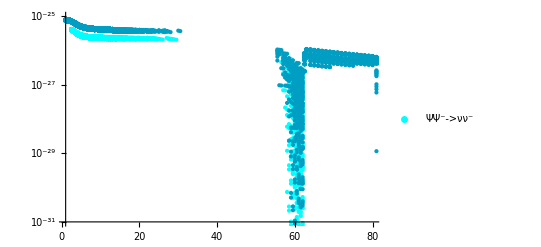

```mathematica
ListLogPlot[{Listsvnn1,Listsvnn2,Listsvnnd1,Listsvnnd2},PlotRange->{{1,80},{10^-31,10^-25}},PlotStyle->{Cyan,Cyan,RGBColor[0,0.62,0.76],RGBColor[0,0.62,0.76]},PlotLegends->Placed[PointLegend[{"ΨΨ^-->νν^-"},LabelStyle->16,LegendFunction->"Frame",Background->White],{0.65,.8}]]
```

```mathematica
Export["SVnunuLux.pdf",fsvnn]
```

SVnunuLux.pdf

Neutrino Flux

```mathematica
km2yeartocm2s=1/(365*24*3600*10^10);
km3yeartocm3s=1/(365*24*3600*10^15);
```

```mathematica
listFluxnuCon1=Table[{omnd1[[i,1]],omnd1[[i,13]]*km3yeartocm3s},{i,1,Length[omnd1]}];
listFluxnuCon22=Table[{omnd2[[i,1]],omnd2[[i,13]]*km3yeartocm3s},{i,1,Length[omnd2]}];
listFluxnuCon2=Table[If[listFluxnuCon22[[i,2]]>=10^-40,{listFluxnuCon22[[i,1]],listFluxnuCon22[[i,2]]},Unevaluated[Sequence[]]],{i,1,Length[listFluxnuCon22]}];
listFluxnuCond1=Table[{omd1[[i,1]],omd1[[i,13]]*km3yeartocm3s},{i,1,Length[omd1]}];
listFluxnuCond22=Table[{omd2[[i,1]],omd2[[i,13]]*km3yeartocm3s},{i,1,Length[omd2]}];
listFluxnuCond2=Table[If[listFluxnuCond22[[i,2]]>=10^-40,{listFluxnuCond22[[i,1]],listFluxnuCond22[[i,2]]},Unevaluated[Sequence[]]],{i,1,Length[listFluxnuCond22]}];
```

```mathematica
Lb1=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCon1[[All,{1,2}]],First]
Lb2=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCon1[[All,{1,2}]],First]
Fb1=Interpolation[Lb1[[All,{1,2}]],InterpolationOrder->2];
Fb2=Interpolation[Lb2[[All,{1,2}]],InterpolationOrder->2];
Lbb1=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCon2[[All,{1,2}]],First]
Lbb2=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCon2[[All,{1,2}]],First]
Fbb1=Interpolation[Lbb1[[All,{1,2}]],InterpolationOrder->2];
Fbb2=Interpolation[Lbb2[[All,{1,2}]],InterpolationOrder->2];
```

{{2.5,4.01763×10^-24},{3.,2.67035×10^-24},{3.5,1.71442×10^-24},{4.,1.45941×10^-24},{4.5,2.16229×10^-24},{5.,1.15665×10^-24},{5.5,1.52952×10^-24},{6.,1.93909×10^-24},{6.5,3.04214×10^-24},{7.,3.49759×10^-24},{7.5,1.74658×10^-24},{8.,1.90462×10^-24},{8.5,2.04953×10^-24},{9.,5.1706×10^-24},{9.5,5.54033×10^-24},{10.,5.89326×10^-24},{10.5,6.22336×10^-24},{11.,5.1132×10^-24},{11.5,5.28634×10^-24},{12.,5.44394×10^-24},{12.5,5.59614×10^-24},{13.,5.73218×10^-24},{13.5,5.85997×10^-24},{14.,1.33004×10^-23},{14.5,1.50666×10^-23},{15.,1.54788×10^-23},{15.5,1.58844×10^-23},{16.,1.62655×10^-23},{16.5,1.66416×10^-23},{17.,1.7195×10^-23},{17.5,1.75086×10^-23},{18.,2.34938×10^-23},{18.5,2.38971×10^-23},{19.,2.59335×10^-23},{19.5,1.35391×10^-23},{20.,1.3751×10^-23},{20.5,1.39618×10^-23},{21.,1.41708×10^-23},{21.5,1.43807×10^-23},{22.,1.45868×10^-23},{22.5,2.87129×10^-23},{23.,2.91657×10^-23},{23.5,2.96176×10^-23},{24.,3.00647×10^-23},{24.5,4.629×10^-23},{25.,4.76218×10^-23},{25.5,4.83321×10^-23},{26.,4.90424×10^-23},{27.,4.14764×10^-23},{27.5,2.86726×10^-23},{28.,2.91533×10^-23},{28.5,2.96382×10^-23},{29.,4.44191×10^-23},{29.5,4.51801×10^-23}}

{{2.5,1.42976×10^-23},{3.,1.60597×10^-23},{3.5,1.54588×10^-23},{4.,1.47191×10^-23},{4.5,1.45817×10^-23},{5.,1.49157×10^-23},{5.5,1.59437×10^-23},{6.,1.70196×10^-23},{6.5,1.88873×10^-23},{7.,2.03244×10^-23},{7.5,2.26072×10^-23},{8.,2.48044×10^-23},{8.5,2.72083×10^-23},{9.,2.9986×10^-23},{9.5,3.28926×10^-23},{10.,3.59272×10^-23},{10.5,3.8946×10^-23},{11.,4.21043×10^-23},{11.5,4.63756×10^-23},{12.,5.01554×10^-23},{12.5,5.39098×10^-23},{13.,5.7807×10^-23},{13.5,5.91451×10^-23},{14.,5.94749×10^-23},{14.5,6.00457×10^-23},{15.,6.1796×10^-23},{15.5,6.07813×10^-23},{16.,5.85616×10^-23},{16.5,6.0144×10^-23},{17.,5.61771×10^-23},{17.5,5.75247×10^-23},{18.,5.88565×10^-23},{18.5,6.00901×10^-23},{19.,6.13648×10^-23},{19.5,5.44362×10^-23},{20.,5.34786×10^-23},{20.5,5.45123×10^-23},{21.,5.55365×10^-23},{21.5,5.65639×10^-23},{22.,4.24404×10^-23},{22.5,4.32046×10^-23},{23.,5.53272×10^-23},{23.5,5.63229×10^-23},{24.,4.6179×10^-23},{24.5,4.68988×10^-23},{25.,4.76218×10^-23},{25.5,4.83321×10^-23},{26.,4.90424×10^-23},{27.,4.14764×10^-23},{27.5,4.21994×10^-23},{28.,4.29351×10^-23},{28.5,4.36739×10^-23},{29.,4.44191×10^-23},{29.5,4.51801×10^-23}}

{{56.5,2.00891×10^-23},{57.,2.58086×10^-24},{57.5,1.71648×10^-24},{58.,3.12319×10^-27},{58.5,3.94882×10^-28},{59.,7.91952×10^-29},{59.5,1.58758×10^-29},{60.,3.36631×10^-30},{60.5,1.13943×10^-30},{61.,4.42859×10^-31},{61.5,3.11117×10^-31},{62.,6.20497×10^-31},{84.,5.9421×10^-27}}

{{56.5,2.00891×10^-23},{57.,1.47251×10^-23},{57.5,3.86986×10^-23},{58.,2.75498×10^-23},{58.5,2.03361×10^-23},{59.,3.0085×10^-23},{59.5,1.27435×10^-23},{60.,1.59966×10^-23},{60.5,2.69042×10^-23},{61.,1.73097×10^-23},{61.5,1.69666×10^-23},{62.,1.70288×10^-23},{84.,5.5749×10^-25}}

{{1.,0.},{1.5,7.46924×10^-29},{2.,5.06754×10^-28},{2.5,3.24137×10^-27},{3.,3.16863×10^-27},{3.5,2.63229×10^-26},{4.,3.01446×10^-26},{4.5,3.62728×10^-26},{5.,5.52226×10^-26},{5.5,1.73335×10^-25},{6.,1.69479×10^-25},{6.5,2.9387×10^-25},{7.,4.33536×10^-25},{7.5,5.03678×10^-25},{8.,7.86783×10^-25},{8.5,3.10524×10^-25},{9.,1.929×10^-24},{9.5,1.75048×10^-24},{10.,1.53834×10^-24},{10.5,1.4818×10^-24},{11.,1.50415×10^-24},{11.5,2.88613×10^-24},{12.,2.70313×10^-24},{12.5,2.57709×10^-24},{13.,2.51608×10^-24},{13.5,2.70307×10^-24},{14.,2.64847×10^-24},{14.5,5.02093×10^-24},{15.,6.44343×10^-24},{15.5,6.45358×10^-24},{16.,6.58581×10^-24},{16.5,6.60483×10^-24},{17.,9.53006×10^-24},{17.5,9.62646×10^-24},{18.,6.01979×10^-24},{18.5,6.05498×10^-24},{19.,6.08828×10^-24},{19.5,1.446×10^-23},{20.,1.46918×10^-23},{20.5,1.50958×10^-23},{21.,1.53123×10^-23},{21.5,2.74033×10^-23},{22.,2.21239×10^-23},{22.5,2.25415×10^-23},{23.,2.29626×10^-23},{23.5,3.2715×10^-23},{24.,3.33492×10^-23},{24.5,4.45745×10^-23},{25.,1.73877×10^-23},{25.5,1.77026×10^-23},{26.,1.80181×10^-23},{26.5,2.54496×10^-23},{27.,3.58828×10^-23},{27.5,3.6536×10^-23},{28.,3.71924×10^-23},{30.,4.4343×10^-23},{30.5,4.46823×10^-23}}

{{1.,0.},{1.5,2.62307×10^-27},{2.,2.54192×10^-26},{2.5,7.29928×10^-26},{3.,1.60173×10^-25},{3.5,1.82132×10^-25},{4.,3.36695×10^-25},{4.5,4.69115×10^-25},{5.,6.37874×10^-25},{5.5,6.39047×10^-25},{6.,9.64168×10^-25},{6.5,1.42938×10^-24},{7.,2.08517×10^-24},{7.5,2.85334×10^-24},{8.,3.94438×10^-24},{8.5,4.8868×10^-24},{9.,6.582×10^-24},{9.5,8.72241×10^-24},{10.,1.07579×10^-23},{10.5,1.32975×10^-23},{11.,1.5852×10^-23},{11.5,1.91026×10^-23},{12.,2.22444×10^-23},{12.5,2.56009×10^-23},{13.,2.94416×10^-23},{13.5,3.3606×10^-23},{14.,3.7741×10^-23},{14.5,4.21518×10^-23},{15.,4.64612×10^-23},{15.5,5.14555×10^-23},{16.,5.30093×10^-23},{16.5,5.51402×10^-23},{17.,5.57078×10^-23},{17.5,5.92656×10^-23},{18.,6.1054×10^-23},{18.5,5.931×10^-23},{19.,6.01788×10^-23},{19.5,6.06481×10^-23},{20.,5.71062×10^-23},{20.5,6.0515×10^-23},{21.,5.33929×10^-23},{21.5,5.62246×10^-23},{22.,5.72901×10^-23},{22.5,5.83428×10^-23},{23.,5.13445×10^-23},{23.5,5.23307×10^-23},{24.,4.40703×10^-23},{24.5,4.45745×10^-23},{25.,4.54401×10^-23},{25.5,2.45691×10^-23},{26.,3.62062×10^-23},{26.5,4.93658×10^-23},{27.,5.02949×10^-23},{27.5,3.6536×10^-23},{28.,3.71924×10^-23},{30.,4.4343×10^-23},{30.5,4.46823×10^-23}}

{{55.5,3.2734×10^-24},{56.,3.23725×10^-24},{56.5,6.15963×10^-24},{57.,5.88914×10^-25},{57.5,5.19692×10^-24},{58.,1.16365×10^-24},{58.5,2.71547×10^-26},{59.,1.69146×10^-27},{59.5,4.10832×10^-28},{60.,8.84069×10^-29},{60.5,2.48256×10^-29},{61.,8.39834×10^-30},{61.5,5.11828×10^-30},{62.,6.38572×10^-30},{62.5,3.84893×10^-25},{63.,2.80898×10^-24},{64.,2.75796×10^-24},{65.,2.70967×10^-24},{66.,2.66324×10^-24},{67.,2.62012×10^-24},{68.,2.57835×10^-24},{69.,2.53869×10^-24},{70.,2.50133×10^-24},{71.,2.45615×10^-24},{72.,2.41359×10^-24},{73.,2.37319×10^-24},{74.,2.33432×10^-24},{75.,2.29801×10^-24},{76.,2.26389×10^-24},{77.,2.23116×10^-24},{78.,2.20028×10^-24},{79.,2.17155×10^-24},{80.,2.14358×10^-24},{81.,1.59012×10^-31},{82.,2.09167×10^-24},{82.5,7.66616×10^-30},{83.,2.06916×10^-24},{84.,2.04262×10^-24},{85.,9.35249×10^-29},{86.,2.00599×10^-24},{87.,1.98808×10^-24},{88.,1.97067×10^-24},{89.,1.95374×10^-24},{90.,1.93788×10^-24},{92.,6.54236×10^-27},{92.5,2.25786×10^-30},{93.,2.21693×10^-30},{95.,1.85369×10^-24},{100.,7.53869×10^-36},{105.,1.69904×10^-24},{110.,1.62335×10^-24},{115.,1.55426×10^-24},{120.,1.48909×10^-24},{125.,9.59316×10^-27},{126.,3.50235×10^-28},{127.,1.31761×10^-30},{130.,2.61847×10^-37},{135.,1.319×10^-24},{140.,2.37865×10^-26},{145.,1.84868×10^-26},{150.,1.16803×10^-24},{155.,8.81532×10^-30},{165.,1.68227×10^-26},{170.,1.63033×10^-26},{175.,1.58232×10^-26},{180.,2.57385×10^-24},{185.,2.35553×10^-28},{190.,2.26728×10^-24},{195.,1.5078×10^-26},{200.,1.09646×10^-26}}

{{55.5,7.9265×10^-23},{56.,4.2545×10^-23},{56.5,4.26148×10^-23},{57.,4.08327×10^-23},{57.5,5.11225×10^-23},{58.,4.03127×10^-23},{58.5,4.01414×10^-23},{59.,3.20142×10^-23},{59.5,2.61219×10^-23},{60.,2.18331×10^-23},{60.5,2.49794×10^-23},{61.,2.46921×10^-23},{61.5,1.6029×10^-23},{62.,1.586×10^-23},{62.5,6.40126×10^-23},{63.,1.53643×10^-22},{64.,1.53209×10^-22},{65.,1.52809×10^-22},{66.,1.52448×10^-22},{67.,1.52102×10^-22},{68.,1.51801×10^-22},{69.,1.51532×10^-22},{70.,1.51294×10^-22},{71.,1.50463×10^-22},{72.,1.49661×10^-22},{73.,1.4889×10^-22},{74.,1.48161×10^-22},{75.,1.47454×10^-22},{76.,1.46772×10^-22},{77.,1.46128×10^-22},{78.,1.91109×10^-22},{79.,1.90411×10^-22},{80.,1.89764×10^-22},{81.,1.89165×10^-22},{82.,1.88575×10^-22},{82.5,4.4882×10^-26},{83.,1.87976×10^-22},{84.,5.60946×10^-23},{85.,5.54129×10^-23},{86.,5.48326×10^-23},{87.,5.42713×10^-23},{88.,5.36974×10^-23},{89.,5.31107×10^-23},{90.,3.55213×10^-23},{92.,7.6855×10^-24},{92.5,3.70846×10^-26},{93.,7.47019×10^-24},{95.,1.92513×10^-23},{100.,8.56101×10^-24},{105.,7.35128×10^-24},{110.,1.62335×10^-24},{115.,1.55426×10^-24},{120.,1.48909×10^-24},{125.,2.03913×10^-24},{126.,7.32782×10^-24},{127.,1.64717×10^-26},{130.,7.4889×10^-24},{135.,1.319×10^-24},{140.,1.41733×10^-24},{145.,1.21693×10^-24},{150.,8.14244×10^-24},{155.,7.7708×10^-24},{165.,3.13074×10^-24},{170.,8.42878×10^-24},{175.,7.66965×10^-24},{180.,6.98535×10^-24},{185.,6.37177×10^-24},{190.,5.82255×10^-24},{195.,5.33486×10^-24},{200.,3.5144×10^-25}}

InterpolatingFunction::dmval: Input value {57.0001} lies outside the range of data in the interpolating function. Extrapolation will be used.

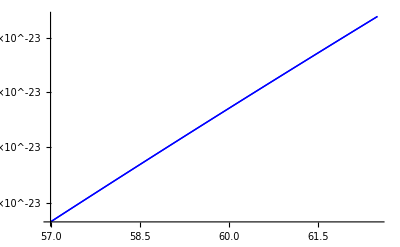

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCond1[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCond1[[All,{1,2}]],First]
fisd2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fisd22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];
see2=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCond2[[All,{1,2}]],First]
ses22=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuCond2[[All,{1,2}]],First]
fised2=Interpolation[see2[[All,{1,2}]],InterpolationOrder->1];
fised22=Interpolation[ses22[[All,{1,2}]],InterpolationOrder->1];
figs1=Show[LogPlot[{fisd2[m],fisd22[m]},{m,57,62.5},PlotStyle->{Blue,Blue},Filling->{2->{1}}]]
```

```mathematica
listFluxnuUp1=Table[{omnd1[[i,1]],omnd1[[i,12]]*km2yeartocm2s},{i,1,Length[omnd1]}];
listFluxnuUp22=Table[{omnd2[[i,1]],omnd2[[i,12]]*km2yeartocm2s},{i,1,Length[omnd2]}];
listFluxnuUp2=Table[If[listFluxnuUp22[[i,2]]>=10^-40,{listFluxnuUp22[[i,1]],listFluxnuUp22[[i,2]]},Unevaluated[Sequence[]]],{i,1,Length[listFluxnuUp22]}];
listFluxnuUpd1=Table[{omd1[[i,1]],omd1[[i,12]]*km2yeartocm2s},{i,1,Length[omd1]}];
listFluxnuUpd22=Table[{omd2[[i,1]],omd2[[i,12]]*km2yeartocm2s},{i,1,Length[omd2]}];
listFluxnuUpd2=Table[If[listFluxnuUpd22[[i,2]]>=10^-40,{listFluxnuUpd22[[i,1]],listFluxnuUpd22[[i,2]]},Unevaluated[Sequence[]]],{i,1,Length[listFluxnuUpd22]}];
```

```mathematica
Lu1=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUp1[[All,{1,2}]],First]
Lu2=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUp1[[All,{1,2}]],First]
Fbu1=Interpolation[Lu1[[All,{1,2}]],InterpolationOrder->2];
Fbu2=Interpolation[Lu2[[All,{1,2}]],InterpolationOrder->2];
Lub1=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUp2[[All,{1,2}]],First];
Lub2=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUp2[[All,{1,2}]],First];
Fbbu1=Interpolation[Lub1[[All,{1,2}]],InterpolationOrder->2];
Fbbu2=Interpolation[Lub2[[All,{1,2}]],InterpolationOrder->2];
```

{{2.5,1.49892×10^-21},{3.,1.33371×10^-21},{3.5,1.07239×10^-21},{4.,1.09624×10^-21},{4.5,1.89476×10^-21},{5.,1.15757×10^-21},{5.5,1.72032×10^-21},{6.,2.41996×10^-21},{6.5,4.1692×10^-21},{7.,5.21911×10^-21},{7.5,2.81719×10^-21},{8.,3.30067×10^-21},{8.5,3.79598×10^-21},{9.,1.01871×10^-20},{9.5,1.15649×10^-20},{10.,1.29845×10^-20},{10.5,1.44283×10^-20},{11.,1.24366×10^-20},{11.5,1.34548×10^-20},{12.,1.44644×10^-20},{12.5,1.54877×10^-20},{13.,1.64916×10^-20},{13.5,1.74937×10^-20},{14.,4.11308×10^-20},{14.5,4.81894×10^-20},{15.,5.1132×10^-20},{15.5,5.41191×10^-20},{16.,5.7084×10^-20},{16.5,6.00932×10^-20},{17.,6.38128×10^-20},{17.5,6.67142×10^-20},{18.,9.18252×10^-20},{18.5,9.5716×10^-20},{19.,1.06361×10^-19},{19.5,5.68113×10^-20},{20.,5.89897×10^-20},{20.5,6.11904×10^-20},{21.,6.34069×10^-20},{21.5,6.5652×10^-20},{22.,6.79033×10^-20},{22.5,1.36216×10^-19},{23.,1.40931×10^-19},{23.5,1.45697×10^-19},{24.,1.50488×10^-19},{24.5,2.35661×10^-19},{25.,2.46471×10^-19},{25.5,2.54205×10^-19},{26.,2.62015×10^-19},{27.,2.28393×10^-19},{27.5,1.60211×10^-19},{28.,1.65243×10^-19},{28.5,1.70351×10^-19},{29.,2.58828×10^-19},{29.5,2.66794×10^-19}}

{{2.5,5.33422×10^-21},{3.,8.02099×10^-21},{3.5,9.6699×10^-21},{4.,1.10563×10^-20},{4.5,1.27775×10^-20},{5.,1.49274×10^-20},{5.5,1.79322×10^-20},{6.,2.12402×10^-20},{6.5,2.58838×10^-20},{7.,3.03276×10^-20},{7.5,3.64663×10^-20},{8.,4.29858×10^-20},{8.5,5.03932×10^-20},{9.,5.90753×10^-20},{9.5,6.86612×10^-20},{10.,7.91603×10^-20},{10.5,9.02968×10^-20},{11.,1.02413×10^-19},{11.5,1.18037×10^-19},{12.,1.3326×10^-19},{12.5,1.49191×10^-19},{13.,1.66315×10^-19},{13.5,1.76566×10^-19},{14.,1.83923×10^-19},{14.5,1.92054×10^-19},{15.,2.04135×10^-19},{15.5,2.07078×10^-19},{16.,2.05527×10^-19},{16.5,2.17184×10^-19},{17.,2.08486×10^-19},{17.5,2.19194×10^-19},{18.,2.30036×10^-19},{18.5,2.40674×10^-19},{19.,2.51677×10^-19},{19.5,2.28418×10^-19},{20.,2.29417×10^-19},{20.5,2.38908×10^-19},{21.,2.485×10^-19},{21.5,2.58229×10^-19},{22.,1.97568×10^-19},{22.5,2.04969×10^-19},{23.,2.67348×10^-19},{23.5,2.77064×10^-19},{24.,2.31152×10^-19},{24.5,2.38759×10^-19},{25.,2.46471×10^-19},{25.5,2.54205×10^-19},{26.,2.62015×10^-19},{27.,2.28393×10^-19},{27.5,2.35797×10^-19},{28.,2.43357×10^-19},{28.5,2.51031×10^-19},{29.,2.58828×10^-19},{29.5,2.66794×10^-19}}

```mathematica
se2=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUpd1[[All,{1,2}]],First]
se22=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUpd1[[All,{1,2}]],First]
fisd2=Interpolation[se2[[All,{1,2}]],InterpolationOrder->1];
fisd22=Interpolation[se22[[All,{1,2}]],InterpolationOrder->1];
see2=(First[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUpd2[[All,{1,2}]],First]
see22=(Last[SortBy[#1,Last]]&)/@SplitBy[listFluxnuUpd2[[All,{1,2}]],First]
fised2=Interpolation[see2[[All,{1,2}]],InterpolationOrder->1];
fised22=Interpolation[see22[[All,{1,2}]],InterpolationOrder->1];
```

{{1.,0.},{1.5,9.00431×10^-27},{2.,1.24971×10^-25},{2.5,1.20928×10^-24},{3.,1.58257×10^-24},{3.5,1.64653×10^-23},{4.,2.26433×10^-23},{4.5,3.17827×10^-23},{5.,5.52638×10^-23},{5.5,1.94955×10^-22},{6.,2.11507×10^-22},{6.5,4.02714×10^-22},{7.,6.46911×10^-22},{7.5,8.12437×10^-22},{8.,1.36349×10^-21},{8.5,5.7512×10^-22},{9.,3.80042×10^-21},{9.5,3.65392×10^-21},{10.,3.38946×10^-21},{10.5,3.43544×10^-21},{11.,3.65868×10^-21},{11.5,7.34589×10^-21},{12.,7.18195×10^-21},{12.5,7.13217×10^-21},{13.,7.23871×10^-21},{13.5,8.06951×10^-21},{14.,8.19064×10^-21},{14.5,1.60588×10^-20},{15.,2.12852×10^-20},{15.5,2.19876×10^-20},{16.,2.31139×10^-20},{16.5,2.38505×10^-20},{17.,3.53691×10^-20},{17.5,3.66819×10^-20},{18.,2.35287×10^-20},{18.5,2.42523×10^-20},{19.,2.49702×10^-20},{19.5,6.06767×10^-20},{20.,6.30264×10^-20},{20.5,6.61625×10^-20},{21.,6.85153×10^-20},{21.5,1.25105×10^-19},{22.,1.0299×10^-19},{22.5,1.06941×10^-19},{23.,1.10959×10^-19},{23.5,1.60937×10^-19},{24.,1.66936×10^-19},{24.5,2.26925×10^-19},{25.,8.99924×10^-20},{25.5,9.31063×10^-20},{26.,9.62646×10^-20},{26.5,1.38064×10^-19},{27.,1.97606×10^-19},{27.5,2.04151×10^-19},{28.,2.10819×10^-19},{30.,2.65306×10^-19},{30.5,2.71353×10^-19}}

{{1.,0.},{1.5,3.16216×10^-25},{2.,6.26871×10^-24},{2.5,2.72327×10^-23},{3.,7.99975×10^-23},{3.5,1.13927×10^-22},{4.,2.52908×10^-22},{4.5,4.11086×10^-22},{5.,6.38382×10^-22},{5.5,7.18766×10^-22},{6.,1.20326×10^-21},{6.5,1.95887×10^-21},{7.,3.11146×10^-21},{7.5,4.60236×10^-21},{8.,6.83568×10^-21},{8.5,9.05093×10^-21},{9.,1.29674×10^-20},{9.5,1.82065×10^-20},{10.,2.37028×10^-20},{10.5,3.08298×10^-20},{11.,3.85591×10^-20},{11.5,4.86206×10^-20},{12.,5.91007×10^-20},{12.5,7.08492×10^-20},{13.,8.47032×10^-20},{13.5,1.00323×10^-19},{14.,1.16711×10^-19},{14.5,1.34817×10^-19},{15.,1.53479×10^-19},{15.5,1.75314×10^-19},{16.,1.86045×10^-19},{16.5,1.99115×10^-19},{17.,2.06748×10^-19},{17.5,2.25821×10^-19},{18.,2.38623×10^-19},{18.5,2.37551×10^-19},{19.,2.46804×10^-19},{19.5,2.54493×10^-19},{20.,2.44984×10^-19},{20.5,2.65224×10^-19},{21.,2.38908×10^-19},{21.5,2.56684×10^-19},{22.,2.66689×10^-19},{22.5,2.76779×10^-19},{23.,2.48097×10^-19},{23.5,2.5742×10^-19},{24.,2.20589×10^-19},{24.5,2.26925×10^-19},{25.,2.35176×10^-19},{25.5,1.29221×10^-19},{26.,1.9343×10^-19},{26.5,2.67815×10^-19},{27.,2.7695×10^-19},{27.5,2.04151×10^-19},{28.,2.10819×10^-19},{30.,2.65306×10^-19},{30.5,2.71353×10^-19}}

{{55.5,3.30416×10^-20},{56.,3.29306×10^-20},{56.5,6.3131×10^-20},{57.,6.08067×10^-21},{57.5,5.40557×10^-20},{58.,1.21921×10^-20},{58.5,2.86593×10^-22},{59.,1.79775×10^-23},{59.5,4.3972×10^-24},{60.,9.52848×10^-25},{60.5,2.69429×10^-25},{61.,9.17681×10^-26},{61.5,5.63071×10^-26},{62.,7.07255×10^-26},{62.5,4.2916×10^-21},{63.,3.15259×10^-20},{64.,3.13562×10^-20},{65.,3.11996×10^-20},{66.,3.10486×10^-20},{67.,3.09209×10^-20},{68.,3.07946×10^-20},{69.,3.06795×10^-20},{70.,3.05797×10^-20},{71.,3.03942×10^-20},{72.,3.02261×10^-20},{73.,3.00707×10^-20},{74.,2.9921×10^-20},{75.,2.97913×10^-20},{76.,2.96778×10^-20},{77.,2.95713×10^-20},{78.,2.94774×10^-20},{79.,2.94029×10^-20},{80.,2.93284×10^-20},{81.,2.19812×10^-27},{82.,2.92076×10^-20},{82.5,1.07588×10^-25},{83.,2.91825×10^-20},{84.,2.90925×10^-20},{85.,1.34497×10^-24},{86.,2.91239×10^-20},{87.,2.91359×10^-20},{88.,2.91489×10^-20},{89.,2.91629×10^-20},{90.,2.91873×10^-20},{92.,1.00371×10^-22},{92.5,3.47983×10^-26},{93.,3.43195×10^-26},{95.,2.92092×10^-20},{100.,1.23912×10^-31},{105.,2.9153×10^-20},{110.,2.90046×10^-20},{115.,2.88508×10^-20},{120.,2.86577×10^-20},{125.,1.91048×10^-22},{126.,7.02118×10^-24},{127.,2.65887×10^-26},{130.,5.38686×10^-33},{135.,2.79823×10^-20},{140.,5.19628×10^-22},{145.,4.1524×10^-22},{150.,2.69384×10^-20},{155.,2.0852×10^-25},{165.,4.17079×10^-22},{170.,4.13179×10^-22},{175.,4.09469×10^-22},{180.,6.79509×10^-20},{185.,6.33942×10^-24},{190.,6.21449×10^-20},{195.,4.20599×10^-22},{200.,3.11019×10^-22}}

{{55.5,8.00165×10^-19},{56.,4.32712×10^-19},{56.5,4.36739×10^-19},{57.,4.21613×10^-19},{57.5,5.3171×10^-19},{58.,4.22374×10^-19},{58.5,4.23611×10^-19},{59.,3.40246×10^-19},{59.5,2.79592×10^-19},{60.,2.35322×10^-19},{60.5,2.71106×10^-19},{61.,2.69828×10^-19},{61.5,1.76338×10^-19},{62.,1.75656×10^-19},{62.5,7.13724×10^-19},{63.,1.72428×10^-18},{64.,1.74182×10^-18},{65.,1.75942×10^-18},{66.,1.77721×10^-18},{67.,1.79493×10^-18},{68.,1.81298×10^-18},{69.,1.83118×10^-18},{70.,1.84957×10^-18},{71.,1.8619×10^-18},{72.,1.87421×10^-18},{73.,1.88657×10^-18},{74.,1.89907×10^-18},{75.,1.91156×10^-18},{76.,1.92402×10^-18},{77.,1.93668×10^-18},{78.,2.56028×10^-18},{79.,2.5781×10^-18},{80.,2.59633×10^-18},{81.,2.61482×10^-18},{82.,2.63318×10^-18},{82.5,6.29883×10^-22},{83.,2.6511×10^-18},{84.,7.98928×10^-19},{85.,7.96899×10^-19},{86.,7.96074×10^-19},{87.,7.95345×10^-19},{88.,7.94267×10^-19},{89.,7.92777×10^-19},{90.,5.34976×10^-19},{92.,1.1791×10^-19},{92.5,5.71537×10^-22},{93.,1.15649×10^-19},{95.,3.03349×10^-19},{100.,1.40715×10^-19},{105.,1.26135×10^-19},{110.,2.90046×10^-20},{115.,2.88508×10^-20},{120.,2.86577×10^-20},{125.,4.06107×10^-20},{126.,1.46902×10^-19},{127.,3.32382×10^-22},{130.,1.54053×10^-19},{135.,2.79823×10^-20},{140.,3.09611×10^-20},{145.,2.73326×10^-20},{150.,1.87795×10^-19},{155.,1.83806×10^-19},{165.,7.76161×10^-20},{170.,2.136×10^-19},{175.,1.98475×10^-19},{180.,1.84424×10^-19},{185.,1.71474×10^-19},{190.,1.59589×10^-19},{195.,1.48808×10^-19},{200.,9.96924×10^-21}}

```mathematica
{{1.,0.},{1.5,9.004312531709792*^-27},{2.,1.2497146118721462*^-25},{2.5,1.2092846270928464*^-24},{3.,1.582572298325723*^-24},{3.5,1.6465309487569762*^-23},{4.,2.2643328259766617*^-23},{4.5,3.1782724505327245*^-23},{5.,5.526382546930492*^-23},{5.5,1.9495497209538305*^-22},{6.,2.1150748351090816*^-22},{6.5,4.027143581938102*^-22},{7.,6.469114662607813*^-22},{7.5,8.124365804160324*^-22},{8.,1.3634893455098934*^-21},{8.5,5.751204972095383*^-22},{9.,3.800418569254185*^-21},{9.5,3.653919330289193*^-21},{10.,3.3894596651445964*^-21},{10.5,3.435438863521055*^-21},{11.,3.658675799086758*^-21},{11.5,7.345890410958904*^-21},{12.,7.18195078640284*^-21},{12.5,7.13216641298833*^-21},{13.,7.238711314053781*^-21},{13.5,8.069507864028411*^-21},{14.,8.190639269406392*^-21},{14.5,1.60587899543379*^-20},{15.,2.1285197869101978*^-20},{15.5,2.1987569761542363*^-20},{16.,2.3113901572805682*^-20},{16.5,2.3850520040588534*^-20},{17.,3.536910197869102*^-20},{17.5,3.6681887366818876*^-20},{18.,2.3528665651953324*^-20},{18.5,2.425228310502283*^-20},{19.,2.4970192795535264*^-20},{19.5,6.067668696093353*^-20},{20.,6.30263825469305*^-20},{20.5,6.616248097412481*^-20},{21.,6.851534753932015*^-20},{21.5,1.2510464231354643*^-19},{22.,1.02990233384069*^-19},{22.5,1.0694127346524606*^-19},{23.,1.1095890410958905*^-19},{23.5,1.609367072552004*^-19},{24.,1.6693619989852866*^-19},{24.5,2.269247843734145*^-19},{25.,8.999238964992389*^-20},{25.5,9.310629122272957*^-20},{26.,9.626458650431253*^-20},{26.5,1.3806443429731102*^-19},{27.,1.9760591070522576*^-19},{27.5,2.0415081177067477*^-19},{28.,2.1081938102486047*^-19},{30.,2.6530631659056316*^-19},{30.5,2.7135337392186706*^-19}}
```

{{1.,0.},{1.5,9.00431×10^-27},{2.,1.24971×10^-25},{2.5,1.20928×10^-24},{3.,1.58257×10^-24},{3.5,1.64653×10^-23},{4.,2.26433×10^-23},{4.5,3.17827×10^-23},{5.,5.52638×10^-23},{5.5,1.94955×10^-22},{6.,2.11507×10^-22},{6.5,4.02714×10^-22},{7.,6.46911×10^-22},{7.5,8.12437×10^-22},{8.,1.36349×10^-21},{8.5,5.7512×10^-22},{9.,3.80042×10^-21},{9.5,3.65392×10^-21},{10.,3.38946×10^-21},{10.5,3.43544×10^-21},{11.,3.65868×10^-21},{11.5,7.34589×10^-21},{12.,7.18195×10^-21},{12.5,7.13217×10^-21},{13.,7.23871×10^-21},{13.5,8.06951×10^-21},{14.,8.19064×10^-21},{14.5,1.60588×10^-20},{15.,2.12852×10^-20},{15.5,2.19876×10^-20},{16.,2.31139×10^-20},{16.5,2.38505×10^-20},{17.,3.53691×10^-20},{17.5,3.66819×10^-20},{18.,2.35287×10^-20},{18.5,2.42523×10^-20},{19.,2.49702×10^-20},{19.5,6.06767×10^-20},{20.,6.30264×10^-20},{20.5,6.61625×10^-20},{21.,6.85153×10^-20},{21.5,1.25105×10^-19},{22.,1.0299×10^-19},{22.5,1.06941×10^-19},{23.,1.10959×10^-19},{23.5,1.60937×10^-19},{24.,1.66936×10^-19},{24.5,2.26925×10^-19},{25.,8.99924×10^-20},{25.5,9.31063×10^-20},{26.,9.62646×10^-20},{26.5,1.38064×10^-19},{27.,1.97606×10^-19},{27.5,2.04151×10^-19},{28.,2.10819×10^-19},{30.,2.65306×10^-19},{30.5,2.71353×10^-19}}

```mathematica
Max[Table[om[[i,13]]*km2yeartocm2s,{i,1,Length[om]}]]
```

1.85325×10^-17

InterpolatingFunction::dmval: Input value {2.00056} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {54.0002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

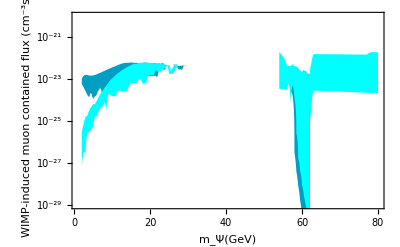

```mathematica
graphflux1=Show[ListLogPlot[{listFluxnuCon1,listFluxnuCon2,listFluxnuCond1,listFluxnuCond2},PlotRange->{{1,80},{10^-29,10^-20}},PlotStyle->{None,None,None,None}],
LogPlot[{Fb1[m],Fb2[m]},{m,2,29.5},PlotStyle->{None,None},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],
LogPlot[{Fbb1[m],Fbb2[m]},{m,56.5,62},PlotStyle->{None,None},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],
LogPlot[{fisd2[m],fisd22[m]},{m,2,30.5},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->Cyan],
LogPlot[{fised2[m],fised22[m]},{m,54,62},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->Cyan],LogPlot[{fised2[m],fised22[m]},{m,62,80},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->Cyan],Frame->True,FrameLabel->{"m_Ψ(GeV)","WIMP-induced \n muon  contained flux (\!\(\*SuperscriptBox[\(cm\), \(-3\)]\)\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["MuonContLux16.png",graphflux1]
```

MuonContLux16.png

```mathematica
ExpandFileName["MuonContLux16.png"]
```

/media/vanniagm/36887AD4887A925B/nu_portal/MATH_NUMODEL/MuonContLux16.png

```mathematica
Export["MuonContLux16.pdf",graphflux1]
```

MuonContLux16.pdf

InterpolatingFunction::dmval: Input value {2.00056} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {54.0002} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

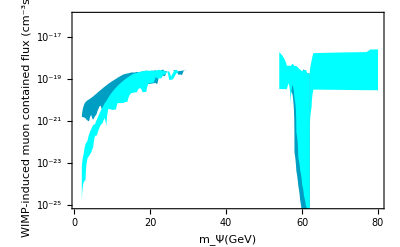

```mathematica
graphflux2=Show[ListLogPlot[{listFluxnuUp1,listFluxnuUp2,listFluxnuUpd1,listFluxnuUpd2},PlotRange->{{1,80},{10^-25,10^-16}},PlotStyle->{None,None,None,None}],
LogPlot[{Fbu1[m],Fbu2[m]},{m,2,29.5},PlotStyle->{None,None},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],
LogPlot[{Fbbu1[m],Fbbu2[m]},{m,56.5,62},PlotStyle->{None,None},Filling->{1->{2}},FillingStyle->RGBColor[0,0.62,0.76]],
LogPlot[{fisd2[m],fisd22[m]},{m,2,30.5},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->Cyan],
LogPlot[{fised2[m],fised22[m]},{m,54,62},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->Cyan],LogPlot[{fised2[m],fised22[m]},{m,62,80},PlotStyle->{None,None},Filling->{2->{1}},FillingStyle->Cyan],Frame->True,FrameLabel->{"m_Ψ(GeV)","WIMP-induced \n muon  contained flux (\!\(\*SuperscriptBox[\(cm\), \(-3\)]\)\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},LabelStyle->{(*FontWeight->"Bold"*)FontSize->20}(*ListLogLogPlot[t3,PlotRange->{{1,200},{0,2*10^10}},PlotStyle->{Blue}]*),PlotRangePadding->0,ImageSize->{GoldenRatio*400,400}]
```

```mathematica
Export["UpMuonLux16.pdf",graphflux2]
```

UpMuonLux16.pdf

```mathematica
Export["UpMuonLux16.png",graphflux2]
```

UpMuonLux16.png

UpMuon.pdf

```mathematica
Export["MuonContLux.pdf",graphflux1]
```

MuonContLux.pdf

MuonCont.pdf

```mathematica
ParentDirectory[]
```

/home/vanniagm/Dropbox/micromegas_3.6.9.2

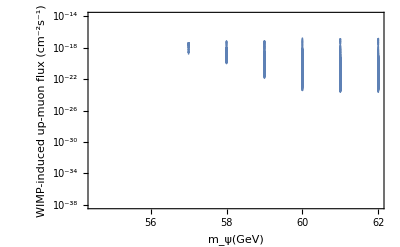

```mathematica
graphflux1=Show[ListLogPlot[Table[{om[[i,1]],om[[i,13]]*km2yeartocm2s},{i,1,Length[om]}],PlotRange->{10^-38,10^-14},Frame->{True,True,False,False},FrameLabel->{"\!\(\*SubscriptBox[\(m\), \(ψ\)]\)(GeV)","WIMP-induced \n up-muon flux (\!\(\*SuperscriptBox[\(cm\), \(-2\)]\)\!\(\*SuperscriptBox[\(s\), \(-1\)]\))"},LabelStyle->{FontWeight->"Bold",FontSize->18}],ImageSize->{GoldenRatio*500,500}]
```

Conversions

Ciii=Sqrt[2]*z3*mudm1/vev;
Cii=2*((Lam^2/vev^2)z3^2mudm3^2/Lam^2+Lx+z3^2*Log[Lam/mphi]);
CViiL=(Lam^2/vev^2)(z3^2 mudm3^2/Lam^2);
CViiR=(Lam^2/vev^2)(z3^2 mudm3^2/Lam^2)(Log[Lam/mphi]);

Higgs decay exluded region

```mathematica
om[[100]]
```

{4.,1000.,100.,13.1,0.3,1.,0.11304,1.1634×10^-46,9.6744×10^-47,1.0805×10^-46,1.7177×10^6,0.000023146,0.0030811,2.4068,0.0073165,0.1732}

```mathematica
Max[Table[(10+om[[i,1]])*om[[i,6]],{i,1,Length[om]}]]
```

288.

```mathematica
Max[Table[om[[i,6]],{i,1,Length[om]}]]
```

4.

```mathematica
vev=246;
```

```mathematica
RegHinv[Lam_,zz_,mu1_,mu3_,Lx_,ms_]:=(vev/Lam)Abs[(zz^2)((mu1^2+mu3^2)/vev^2+Lx*Log[Lam/ms])];
```

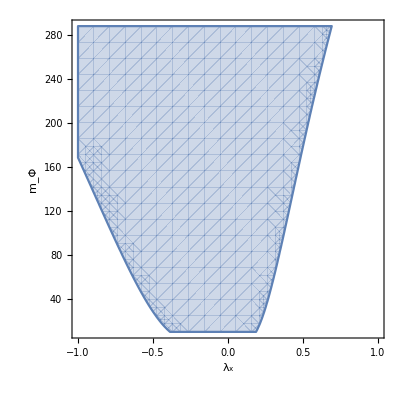

```mathematica
plot1=RegionPlot[RegHinv[1000,2,118,118,lx,ms]<1.3,{lx,-1,1},{ms,10,288},Frame->True,FrameLabel->{"λ_x","m_Φ",None,None}]
```

```mathematica
Export["plot1.pdf",plot1]
```

plot1.pdf

```mathematica
vev=246;
```

```mathematica
RegHinv[Lam_,zz_,mu1_,mu3_,Lx_,ms_]:=(vev/Lam)Abs[(zz^2)((mu1^2+mu3^2)/vev^2+Lx*Log[Lam/ms])];
```

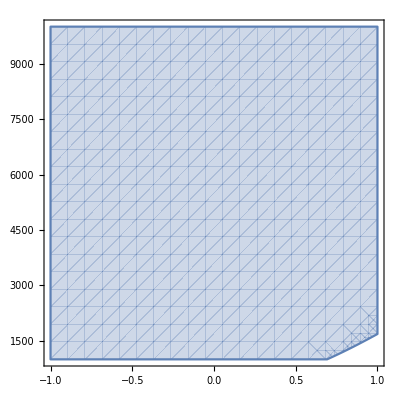

```mathematica
RegionPlot[RegHinv[Lam,2,118,118,lx,288]<1.3,{lx,-1,1},{Lam,1000,10000}]
```

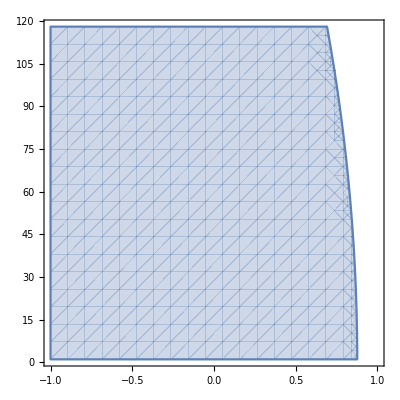

```mathematica
RegionPlot[RegHinv[1000,2,mu,118,lx,288]<1.3,{lx,-1,1},{mu,1,118}]
```

```mathematica
Sqrt[.0022/(125/(512*Pi^5))]
```

1.6606